# Optimizing QSAR with DFT Variables

#### A validation of the Results from Aouidate, et al. “Combining DFT and QSAR studies for predicting psychotomimeticactivity of substituted phenethylamines using statistical methods.” Journal of Taibah University for Science 10 (2016): 787-96.

## Background

The medicinal value of drugs is optimized via Quantitative Structure-Activity Relationships, or QSAR. QSAR seeks to explain the variation in the biological activity of related molecules via variations in their structure and physicochemical properties. Synthesizing and testing new compounds is time-consuming and expensive, so the faster we can reach a mathematical model with predictive power, the better. The physicochemical properties of compounds used in such studies are ultimately a function of the compounds’ electronic structure. The electronic structure of molecules can be computed using Density Functional Theory, or DFT. This is a computationally intensive process, but newer software is becoming more efficient and accessible. Aouidate, et al collected from the literature the biochemical activities of 46 phenalkylamines, a frequently-abused class of psychoactive drugs. They calculated the DFT parameters Etotal, Ehomo, Elumo, dipole moment (DM), and absolute hardness (η), and physicochemical properties such as molecular weight, density, and octanol/water partition coefficient (logP). For phenalkylamines, biological activity is expressed in Mescaline Units (logUM).

## Code

### Importing Data

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/themarchhare/Documents/GitHub/Project/Molecular Structures Real

```mathematica
dataFile=FileNameJoin[{NotebookDirectory[],"Table of Aouidate data.xlsx"}]
```

/Users/themarchhare/Documents/GitHub/Project/Molecular Structures Real/Table of Aouidate data.xlsx

```mathematica
data1=Import[dataFile];
```

```mathematica
firstSheet1=Part[data1,1];
(*displaying the order of the variable columns for future reference*)
```

```mathematica
firstSheet1[[1]]
```

{logMU,ET,IP,EHOMO,η,ELUMO,DM,Qp,Qmin,MW,n,γ,D,logP,}

```mathematica
(*At this stage I'm assigning a variable to all the rows of the imported matrix that actually have numerical data in them. I'm leaving out the row of variable names and the 14 empty rows we accidentally picked up. I'm putting semicolons at the end to collapse the output once I've verified that it's correct.*)
```

```mathematica
firstData1=Part[firstSheet1,2;;-18];
```

```mathematica
(*Now I will make sure that everything is read as a number (expression) rather than a string*)
actualData4=ReplaceAll[firstData1,s_String :>ToExpression[s]];
```

```mathematica
ActualData=actualData4[[All,1;;-2]];
```

```mathematica
transpose=Transpose[ActualData];
```

```mathematica
ToNormalize=transpose[[2;;-1]]
```

(-82328.7 | -30241. | -19406.4 | -20476.1 | -18336.7 | -31310.7 | -86156.7 | -21545.9 | -29171.2 | -29171. | -20382.8 | -18336.6 | -30240.9 | -17266.8 | -22396.4 | -21452.6 | -28101.4 | -19280.5 | -21452.6 | -19280.5 | -22522.4 | -20382.8 | -23498.6 | -21452.5 | -29171. | -29171. | -28101.4 | -22396.4 | -29171. | -30240.9 | -17266.9 | -12104.5 | -31310.5 | -26669.7 | -19280.5 | -16164.5 | -22522.2 | -30240.9 | -30240.9 | -20382.8 | -21452.6 | -20382.7 | -19312.9 | -19312.8 | -17266.8 | -16196.9
7.374 | 7.125 | 6.731 | 6.724 | 6.765 | 7.238 | 7.374 | 6.721 | 7.121 | 6.993 | 6.83 | 6.802 | 7.156 | 8.353 | 7.075 | 6.803 | 7.292 | 7.265 | 7.265 | 6.803 | 6.911 | 7.265 | 7.374 | 7.183 | 7.129 | 7.102 | 7.319 | 7.02 | 7.047 | 7.02 | 7.047 | 7.809 | 7.02 | 7.238 | 7.211 | 7.211 | 7.156 | 7.02 | 7.156 | 7.319 | 7.129 | 7.238 | 7.319 | 7.456 | 7.292 | 7.292
-5.682 | -5.428 | -5.029 | -5.037 | -5.009 | -4.78 | -5.687 | -5.025 | -5.453 | -5.327 | -5.101 | -5.024 | -5.333 | -5.142 | -5.349 | -5.073 | -5.423 | -5.393 | -5.505 | -4.968 | -5.063 | -5.505 | -5.703 | -5.443 | -5.499 | -5.569 | -5.536 | -5.281 | -5.407 | -5.303 | -5.243 | -5.971 | -5.311 | -5.59 | -5.328 | -5.293 | -5.435 | -5.247 | -5.533 | -5.524 | -5.41 | -5.481 | -5.523 | -5.719 | -5.444 | -5.443
5.522 | 5.258 | 5.302 | 5.295 | 5.282 | 5.066 | 5.527 | 5.3 | 5.295 | 5.234 | 5.576 | 5.301 | 5.236 | 5.451 | 5.755 | 5.531 | 5.335 | 5.876 | 5.911 | 5.226 | 5.528 | 5.908 | 5.961 | 5.831 | 5.468 | 5.499 | 5.488 | 5.594 | 5.332 | 5.221 | 5.765 | 6.34 | 5.224 | 5.669 | 5.872 | 5.602 | 5.827 | 5.533 | 5.466 | 5.912 | 5.794 | 5.872 | 5.914 | 6.007 | 5.849 | 5.848
-0.16 | -0.17 | 0.273 | 0.258 | 0.273 | 0.286 | -0.16 | 0.275 | -0.158 | -0.093 | 0.475 | 0.278 | -0.097 | 0.309 | 0.407 | 0.458 | -0.088 | 0.483 | 0.406 | 0.258 | 0.465 | 0.403 | 0.257 | 0.389 | -0.03 | -0.07 | -0.049 | 0.313 | -0.075 | -0.082 | 0.522 | 0.37 | -0.088 | 0.079 | 0.544 | 0.309 | 0.391 | 0.286 | -0.067 | 0.388 | 0.384 | 0.39 | 0.391 | 0.288 | 0.405 | 0.406
3.242 | 1.996 | 1.234 | 1.283 | 1.117 | 2.498 | 3.271 | 1.25 | 2.115 | 4.017 | 3.159 | 1.323 | 4.084 | 1.618 | 1.297 | 3.234 | 4.378 | 1.539 | 3.041 | 1.505 | 3.276 | 3.089 | 1.288 | 2.994 | 3.92 | 3.714 | 4.009 | 0.427 | 4.42 | 4.043 | 2.553 | 1.567 | 4.067 | 3.375 | 1.369 | 1.899 | 2.947 | 3.05 | 3.751 | 3.136 | 2.979 | 3.237 | 3.203 | 1.449 | 3.673 | 3.724
0.046 | 0.135 | 0.126 | 0.126 | 0.127 | -0.15 | 0.046 | 0.122 | -0.131 | -0.219 | 0.349 | 0.125 | -0.22 | 0.133 | 0.273 | 0.353 | -0.223 | 0.326 | 0.265 | 0.326 | 0.352 | 0.225 | 0.269 | 0.264 | 0.293 | 0.289 | 0.293 | 0.283 | -0.226 | -0.222 | 0.378 | 0.179 | -0.219 | 0.267 | 0.265 | 0.329 | 0.265 | 0.3 | 0.285 | 0.245 | 0.26 | 0.249 | 0.253 | 0.305 | 0.308 | 0.307
-0.707 | -0.708 | -0.712 | -0.709 | -0.71 | -0.712 | -0.709 | -0.713 | -0.707 | -0.713 | -0.713 | -0.716 | -0.707 | -0.714 | -0.713 | -0.707 | -0.708 | -0.707 | -0.713 | -0.715 | -0.713 | -0.714 | -0.714 | -0.714 | -0.712 | -0.708 | -0.702 | -0.702 | -0.705 | -0.713 | -0.713 | -0.707 | -0.712 | -0.712 | -0.713 | -0.708 | -0.713 | -0.711 | -0.71 | -0.719 | -0.713 | -0.713 | -0.707 | -0.71 | -0.717 | -0.713
274.154 | 255.376 | 223.311 | 237.338 | 209.285 | 269.403 | 260.128 | 251.365 | 241.35 | 241.35 | 225.284 | 209.285 | 255.376 | 195.258 | 239.268 | 239.311 | 227.323 | 209.242 | 239.311 | 209.242 | 253.337 | 225.284 | 255.31 | 239.311 | 241.35 | 241.35 | 227.323 | 239.268 | 241.35 | 255.376 | 195.258 | 149.233 | 269.403 | 301.38 | 209.242 | 179.216 | 253.337 | 255.376 | 255.376 | 225.284 | 239.311 | 225.284 | 211.258 | 211.258 | 195.258 | 181.232
1.54 | 1.545 | 1.509 | 1.507 | 1.511 | 1.539 | 1.548 | 1.504 | 1.55 | 1.552 | 1.507 | 1.514 | 1.547 | 1.516 | 1.54 | 1.504 | 1.559 | 1.55 | 1.504 | 1.55 | 1.502 | 1.508 | 1.503 | 1.506 | 1.552 | 1.552 | 1.559 | 1.54 | 1.552 | 1.547 | 1.512 | 1.525 | 1.543 | 1.555 | 1.55 | 1.564 | 1.503 | 1.547 | 1.547 | 1.507 | 1.506 | 1.508 | 1.511 | 1.511 | 1.512 | 1.517
37.9 | 42.6 | 33.9 | 33.9 | 34.2 | 41.2 | 39.5 | 33.9 | 43.1 | 44.2 | 34.3 | 34.9 | 43.6 | 35.3 | 43.5 | 34.3 | 45. | 45.4 | 34.3 | 45.4 | 34.2 | 35.2 | 34. | 35.1 | 44.2 | 44.2 | 45. | 43.5 | 44.2 | 43.6 | 34.7 | 35.2 | 43.1 | 39.8 | 45.4 | 48. | 35. | 43.6 | 43.6 | 34.3 | 35.1 | 35.2 | 35.4 | 35.4 | 34.7 | 36.
1.324 | 1.08 | 0.998 | 0.998 | 1.01 | 1.07 | 1.368 | 0.979 | 1.1 | 1.1 | 1.048 | 1.012 | 1.09 | 1.026 | 1.184 | 1.034 | 1.12 | 1.175 | 1.034 | 1.175 | 1.022 | 1.05 | 1.069 | 1.036 | 1.1 | 1.1 | 1.12 | 1.184 | 1.1 | 1.09 | 1.023 | 0.938 | 1.07 | 1.093 | 1.175 | 1.163 | 1.023 | 1.09 | 1.09 | 1.048 | 1.036 | 1.05 | 1.067 | 1.067 | 1.023 | 1.041
2.455 | 2.452 | 2.778 | 3.307 | 2.249 | 2.761 | 2.146 | 3.386 | 1.923 | 1.743 | 1.392 | 2.469 | 2.272 | 1.94 | 1.644 | 1.921 | 1.214 | 1.699 | 1.571 | 1.699 | 2.45 | 1.262 | 0.637 | -1.842 | 1.248 | -1.003 | 0.719 | 1.294 | 1.743 | 2.272 | -1.265 | 2.241 | 2.801 | 2.81 | 1.699 | 1.707 | 1.777 | 1.777 | 1.777 | 1.042 | 1.273 | 0.744 | 0.215 | -3.08 | 0.435 | 0.126)

```mathematica
rationormalize[list_,pos_:43]:=list/list⟦pos⟧
```

```mathematica
RatioNormalizedData=Map[rationormalize,ToNormalize]
```

(4.26288 | 1.56584 | 1.00484 | 1.06023 | 0.949452 | 1.62123 | 4.46109 | 1.11562 | 1.51045 | 1.51044 | 1.0554 | 0.949447 | 1.56584 | 0.894055 | 1.15966 | 1.11079 | 1.45506 | 0.998319 | 1.11079 | 0.998323 | 1.16618 | 1.0554 | 1.21673 | 1.11078 | 1.51044 | 1.51044 | 1.45506 | 1.15966 | 1.51044 | 1.56584 | 0.894061 | 0.626755 | 1.62122 | 1.38093 | 0.998319 | 0.836977 | 1.16617 | 1.56584 | 1.56584 | 1.0554 | 1.11079 | 1.05539 | 1. | 0.999993 | 0.894052 | 0.838658
1.00751 | 0.973494 | 0.919661 | 0.918705 | 0.924307 | 0.988933 | 1.00751 | 0.918295 | 0.972947 | 0.955458 | 0.933188 | 0.929362 | 0.977729 | 1.14128 | 0.966662 | 0.929499 | 0.996311 | 0.992622 | 0.992622 | 0.929499 | 0.944255 | 0.992622 | 1.00751 | 0.981418 | 0.97404 | 0.970351 | 1. | 0.959147 | 0.962836 | 0.959147 | 0.962836 | 1.06695 | 0.959147 | 0.988933 | 0.985244 | 0.985244 | 0.977729 | 0.959147 | 0.977729 | 1. | 0.97404 | 0.988933 | 1. | 1.01872 | 0.996311 | 0.996311
1.02879 | 0.982799 | 0.910556 | 0.912004 | 0.906935 | 0.865472 | 1.02969 | 0.909832 | 0.987326 | 0.964512 | 0.923592 | 0.909651 | 0.965598 | 0.931016 | 0.968495 | 0.918523 | 0.981894 | 0.976462 | 0.996741 | 0.899511 | 0.916712 | 0.996741 | 1.03259 | 0.985515 | 0.995655 | 1.00833 | 1.00235 | 0.956183 | 0.978997 | 0.960167 | 0.949303 | 1.08112 | 0.961615 | 1.01213 | 0.964693 | 0.958356 | 0.984067 | 0.950027 | 1.00181 | 1.00018 | 0.97954 | 0.992395 | 1. | 1.03549 | 0.985696 | 0.985515
0.933717 | 0.889077 | 0.896517 | 0.895333 | 0.893135 | 0.856611 | 0.934562 | 0.896179 | 0.895333 | 0.885019 | 0.942847 | 0.896348 | 0.885357 | 0.921711 | 0.973115 | 0.935238 | 0.902097 | 0.993575 | 0.999493 | 0.883666 | 0.934731 | 0.998985 | 1.00795 | 0.985966 | 0.924586 | 0.929828 | 0.927968 | 0.945891 | 0.901589 | 0.88282 | 0.974806 | 1.07203 | 0.883328 | 0.958573 | 0.992898 | 0.947244 | 0.985289 | 0.935577 | 0.924248 | 0.999662 | 0.979709 | 0.992898 | 1. | 1.01573 | 0.989009 | 0.98884
-0.409207 | -0.434783 | 0.69821 | 0.659847 | 0.69821 | 0.731458 | -0.409207 | 0.703325 | -0.404092 | -0.237852 | 1.21483 | 0.710997 | -0.248082 | 0.790281 | 1.04092 | 1.17136 | -0.225064 | 1.23529 | 1.03836 | 0.659847 | 1.18926 | 1.03069 | 0.657289 | 0.994885 | -0.0767263 | -0.179028 | -0.12532 | 0.800512 | -0.191816 | -0.209719 | 1.33504 | 0.946292 | -0.225064 | 0.202046 | 1.3913 | 0.790281 | 1. | 0.731458 | -0.171355 | 0.992327 | 0.982097 | 0.997442 | 1. | 0.736573 | 1.03581 | 1.03836
1.01218 | 0.623166 | 0.385264 | 0.400562 | 0.348736 | 0.779894 | 1.02123 | 0.390259 | 0.660318 | 1.25414 | 0.986263 | 0.41305 | 1.27505 | 0.505151 | 0.404933 | 1.00968 | 1.36684 | 0.480487 | 0.949422 | 0.469872 | 1.02279 | 0.964408 | 0.402123 | 0.934749 | 1.22385 | 1.15954 | 1.25164 | 0.133313 | 1.37996 | 1.26225 | 0.797065 | 0.489229 | 1.26975 | 1.0537 | 0.427412 | 0.592882 | 0.920075 | 0.952232 | 1.17109 | 0.979082 | 0.930066 | 1.01062 | 1. | 0.452388 | 1.14674 | 1.16266
0.181818 | 0.533597 | 0.498024 | 0.498024 | 0.501976 | -0.592885 | 0.181818 | 0.482213 | -0.517787 | -0.865613 | 1.37945 | 0.494071 | -0.869565 | 0.525692 | 1.07905 | 1.39526 | -0.881423 | 1.28854 | 1.04743 | 1.28854 | 1.3913 | 0.889328 | 1.06324 | 1.04348 | 1.1581 | 1.14229 | 1.1581 | 1.11858 | -0.893281 | -0.87747 | 1.49407 | 0.70751 | -0.865613 | 1.05534 | 1.04743 | 1.3004 | 1.04743 | 1.18577 | 1.12648 | 0.968379 | 1.02767 | 0.98419 | 1. | 1.20553 | 1.21739 | 1.21344
1. | 1.00141 | 1.00707 | 1.00283 | 1.00424 | 1.00707 | 1.00283 | 1.00849 | 1. | 1.00849 | 1.00849 | 1.01273 | 1. | 1.0099 | 1.00849 | 1. | 1.00141 | 1. | 1.00849 | 1.01132 | 1.00849 | 1.0099 | 1.0099 | 1.0099 | 1.00707 | 1.00141 | 0.992928 | 0.992928 | 0.997171 | 1.00849 | 1.00849 | 1. | 1.00707 | 1.00707 | 1.00849 | 1.00141 | 1.00849 | 1.00566 | 1.00424 | 1.01697 | 1.00849 | 1.00849 | 1. | 1.00424 | 1.01414 | 1.00849
1.29772 | 1.20883 | 1.05705 | 1.12345 | 0.990661 | 1.27523 | 1.23133 | 1.18985 | 1.14244 | 1.14244 | 1.06639 | 0.990661 | 1.20883 | 0.924263 | 1.13259 | 1.13279 | 1.07604 | 0.990457 | 1.13279 | 0.990457 | 1.19918 | 1.06639 | 1.20852 | 1.13279 | 1.14244 | 1.14244 | 1.07604 | 1.13259 | 1.14244 | 1.20883 | 0.924263 | 0.706402 | 1.27523 | 1.4266 | 0.990457 | 0.848328 | 1.19918 | 1.20883 | 1.20883 | 1.06639 | 1.13279 | 1.06639 | 1. | 1. | 0.924263 | 0.85787
1.01919 | 1.0225 | 0.998676 | 0.997353 | 1. | 1.01853 | 1.02449 | 0.995367 | 1.02581 | 1.02713 | 0.997353 | 1.00199 | 1.02383 | 1.00331 | 1.01919 | 0.995367 | 1.03177 | 1.02581 | 0.995367 | 1.02581 | 0.994044 | 0.998015 | 0.994705 | 0.996691 | 1.02713 | 1.02713 | 1.03177 | 1.01919 | 1.02713 | 1.02383 | 1.00066 | 1.00927 | 1.02118 | 1.02912 | 1.02581 | 1.03508 | 0.994705 | 1.02383 | 1.02383 | 0.997353 | 0.996691 | 0.998015 | 1. | 1. | 1.00066 | 1.00397
1.07062 | 1.20339 | 0.957627 | 0.957627 | 0.966102 | 1.16384 | 1.11582 | 0.957627 | 1.21751 | 1.24859 | 0.968927 | 0.985876 | 1.23164 | 0.997175 | 1.22881 | 0.968927 | 1.27119 | 1.28249 | 0.968927 | 1.28249 | 0.966102 | 0.99435 | 0.960452 | 0.991525 | 1.24859 | 1.24859 | 1.27119 | 1.22881 | 1.24859 | 1.23164 | 0.980226 | 0.99435 | 1.21751 | 1.12429 | 1.28249 | 1.35593 | 0.988701 | 1.23164 | 1.23164 | 0.968927 | 0.991525 | 0.99435 | 1. | 1. | 0.980226 | 1.01695
1.24086 | 1.01218 | 0.935333 | 0.935333 | 0.946579 | 1.00281 | 1.2821 | 0.917526 | 1.03093 | 1.03093 | 0.982193 | 0.948454 | 1.02156 | 0.961575 | 1.10965 | 0.969072 | 1.04967 | 1.10122 | 0.969072 | 1.10122 | 0.957826 | 0.984067 | 1.00187 | 0.970947 | 1.03093 | 1.03093 | 1.04967 | 1.10965 | 1.03093 | 1.02156 | 0.958763 | 0.8791 | 1.00281 | 1.02437 | 1.10122 | 1.08997 | 0.958763 | 1.02156 | 1.02156 | 0.982193 | 0.970947 | 0.984067 | 1. | 1. | 0.958763 | 0.975633
11.4186 | 11.4047 | 12.9209 | 15.3814 | 10.4605 | 12.8419 | 9.9814 | 15.7488 | 8.94419 | 8.10698 | 6.47442 | 11.4837 | 10.5674 | 9.02326 | 7.64651 | 8.93488 | 5.64651 | 7.90233 | 7.30698 | 7.90233 | 11.3953 | 5.86977 | 2.96279 | -8.56744 | 5.80465 | -4.66512 | 3.34419 | 6.0186 | 8.10698 | 10.5674 | -5.88372 | 10.4233 | 13.0279 | 13.0698 | 7.90233 | 7.93953 | 8.26512 | 8.26512 | 8.26512 | 4.84651 | 5.92093 | 3.46047 | 1. | -14.3256 | 2.02326 | 0.586047)

```mathematica
transform2[n_]:=Log[n+15]
```

```mathematica
logNormalize[n_]:=Log[n]
```

```mathematica
logNormalize[3]
```

Log[3]

```mathematica
ClearAll[logNormalize]
```

```mathematica
log2[n_,c_]:=Log[n+c]
```

```mathematica
log2[3.1,3.2]
```

1.84055

```mathematica
log2[{1.3,4.3},2.1]
```

{1.22378,1.8563}

```mathematica
Log[1.3+2.1]
```

1.22378

```mathematica
Log[4.3+2.1]
```

1.8563

```mathematica
log2[{{1.3,2.9,3.5},{2.1,4.2,4.7},{2.5,3.1,9.0}},1]
```

{{0.832909,1.36098,1.50408},{1.1314,1.64866,1.74047},{1.25276,1.41099,2.30259}}

```mathematica
Log[4.26288+15]
```

2.95818

```mathematica
ClearAll[logNormalize]
```

```mathematica
Log[6.3]
```

1.84055

```mathematica
SetAttributes[transform2,Listable]
```

```mathematica
LogNormedData=log2[RatioNormalizedData,15]
```

(2.95818 | 2.80734 | 2.77289 | 2.77635 | 2.76942 | 2.81068 | 2.96842 | 2.77979 | 2.80399 | 2.80399 | 2.77605 | 2.76942 | 2.80734 | 2.76595 | 2.78252 | 2.77949 | 2.80063 | 2.77248 | 2.77949 | 2.77248 | 2.78292 | 2.77605 | 2.78604 | 2.77949 | 2.80399 | 2.80399 | 2.80063 | 2.78252 | 2.80399 | 2.80734 | 2.76595 | 2.74898 | 2.81068 | 2.79612 | 2.77248 | 2.76235 | 2.78292 | 2.80734 | 2.80734 | 2.77604 | 2.77949 | 2.77604 | 2.77259 | 2.77259 | 2.76594 | 2.76245
2.77306 | 2.77093 | 2.76755 | 2.76749 | 2.76785 | 2.7719 | 2.77306 | 2.76747 | 2.7709 | 2.7698 | 2.7684 | 2.76816 | 2.7712 | 2.78138 | 2.7705 | 2.76817 | 2.77236 | 2.77213 | 2.77213 | 2.76817 | 2.7691 | 2.77213 | 2.77306 | 2.77143 | 2.77096 | 2.77073 | 2.77259 | 2.77003 | 2.77026 | 2.77003 | 2.77026 | 2.77676 | 2.77003 | 2.7719 | 2.77167 | 2.77167 | 2.7712 | 2.77003 | 2.7712 | 2.77259 | 2.77096 | 2.7719 | 2.77259 | 2.77376 | 2.77236 | 2.77236
2.77439 | 2.77151 | 2.76698 | 2.76707 | 2.76676 | 2.76415 | 2.77444 | 2.76694 | 2.7718 | 2.77037 | 2.7678 | 2.76693 | 2.77044 | 2.76827 | 2.77062 | 2.76748 | 2.77146 | 2.77112 | 2.77239 | 2.76629 | 2.76737 | 2.77239 | 2.77462 | 2.77168 | 2.77232 | 2.77311 | 2.77274 | 2.76985 | 2.77128 | 2.7701 | 2.76942 | 2.77765 | 2.77019 | 2.77335 | 2.77038 | 2.76998 | 2.77159 | 2.76946 | 2.7727 | 2.7726 | 2.77131 | 2.77211 | 2.77259 | 2.7748 | 2.77169 | 2.77168
2.76844 | 2.76563 | 2.7661 | 2.76603 | 2.76589 | 2.76359 | 2.76849 | 2.76608 | 2.76603 | 2.76538 | 2.76901 | 2.76609 | 2.7654 | 2.76768 | 2.77091 | 2.76853 | 2.76645 | 2.77219 | 2.77256 | 2.76529 | 2.7685 | 2.77253 | 2.77309 | 2.77171 | 2.76786 | 2.76819 | 2.76808 | 2.7692 | 2.76642 | 2.76524 | 2.77101 | 2.77708 | 2.76527 | 2.77 | 2.77214 | 2.76929 | 2.77167 | 2.76855 | 2.76784 | 2.77257 | 2.77132 | 2.77214 | 2.77259 | 2.77357 | 2.7719 | 2.77189
2.68039 | 2.67864 | 2.75355 | 2.7511 | 2.75355 | 2.75566 | 2.68039 | 2.75387 | 2.68074 | 2.69207 | 2.78593 | 2.75436 | 2.69137 | 2.75939 | 2.77514 | 2.78324 | 2.69293 | 2.78719 | 2.77498 | 2.7511 | 2.78435 | 2.77451 | 2.75094 | 2.77227 | 2.70292 | 2.69604 | 2.69966 | 2.76004 | 2.69518 | 2.69397 | 2.79331 | 2.76923 | 2.69293 | 2.72143 | 2.79675 | 2.75939 | 2.77259 | 2.75566 | 2.69656 | 2.77211 | 2.77147 | 2.77243 | 2.77259 | 2.75599 | 2.77482 | 2.77498
2.77335 | 2.74875 | 2.73341 | 2.7344 | 2.73103 | 2.75874 | 2.77391 | 2.73373 | 2.75113 | 2.78835 | 2.77173 | 2.73521 | 2.78963 | 2.74117 | 2.73469 | 2.77319 | 2.79526 | 2.73958 | 2.76942 | 2.73889 | 2.77401 | 2.77036 | 2.73451 | 2.7685 | 2.78648 | 2.78251 | 2.78819 | 2.7169 | 2.79606 | 2.78885 | 2.75982 | 2.74014 | 2.78931 | 2.77594 | 2.73615 | 2.74681 | 2.76758 | 2.7696 | 2.78323 | 2.77128 | 2.76821 | 2.77325 | 2.77259 | 2.73776 | 2.78172 | 2.7827
2.7201 | 2.74301 | 2.74071 | 2.74071 | 2.74097 | 2.66772 | 2.7201 | 2.73969 | 2.67292 | 2.64861 | 2.79603 | 2.74046 | 2.64833 | 2.7425 | 2.77752 | 2.79699 | 2.64749 | 2.79046 | 2.77555 | 2.79046 | 2.79675 | 2.76565 | 2.77653 | 2.7753 | 2.78242 | 2.78144 | 2.78242 | 2.77997 | 2.64665 | 2.64777 | 2.803 | 2.75414 | 2.64861 | 2.77604 | 2.77555 | 2.79119 | 2.77555 | 2.78413 | 2.78046 | 2.77061 | 2.77432 | 2.7716 | 2.77259 | 2.78535 | 2.78608 | 2.78584
2.77259 | 2.77268 | 2.77303 | 2.77277 | 2.77285 | 2.77303 | 2.77277 | 2.77312 | 2.77259 | 2.77312 | 2.77312 | 2.77338 | 2.77259 | 2.77321 | 2.77312 | 2.77259 | 2.77268 | 2.77259 | 2.77312 | 2.7733 | 2.77312 | 2.77321 | 2.77321 | 2.77321 | 2.77303 | 2.77268 | 2.77215 | 2.77215 | 2.77241 | 2.77312 | 2.77312 | 2.77259 | 2.77303 | 2.77303 | 2.77312 | 2.77268 | 2.77312 | 2.77294 | 2.77285 | 2.77365 | 2.77312 | 2.77312 | 2.77259 | 2.77285 | 2.77347 | 2.77312
2.79103 | 2.78556 | 2.77615 | 2.78027 | 2.772 | 2.78964 | 2.78694 | 2.78438 | 2.78145 | 2.78145 | 2.77673 | 2.772 | 2.78556 | 2.76784 | 2.78084 | 2.78085 | 2.77733 | 2.77199 | 2.78085 | 2.77199 | 2.78496 | 2.77673 | 2.78554 | 2.78085 | 2.78145 | 2.78145 | 2.77733 | 2.78084 | 2.78145 | 2.78556 | 2.76784 | 2.75407 | 2.78964 | 2.7989 | 2.77199 | 2.76306 | 2.78496 | 2.78556 | 2.78556 | 2.77673 | 2.78085 | 2.77673 | 2.77259 | 2.77259 | 2.76784 | 2.76367
2.77379 | 2.77399 | 2.77251 | 2.77242 | 2.77259 | 2.77375 | 2.77412 | 2.7723 | 2.7742 | 2.77428 | 2.77242 | 2.77271 | 2.77408 | 2.7728 | 2.77379 | 2.7723 | 2.77457 | 2.7742 | 2.7723 | 2.7742 | 2.77222 | 2.77246 | 2.77226 | 2.77238 | 2.77428 | 2.77428 | 2.77457 | 2.77379 | 2.77428 | 2.77408 | 2.77263 | 2.77317 | 2.77391 | 2.77441 | 2.7742 | 2.77478 | 2.77226 | 2.77408 | 2.77408 | 2.77242 | 2.77238 | 2.77246 | 2.77259 | 2.77259 | 2.77263 | 2.77284
2.77699 | 2.78522 | 2.76994 | 2.76994 | 2.77047 | 2.78278 | 2.7798 | 2.76994 | 2.78609 | 2.78801 | 2.77064 | 2.77171 | 2.78696 | 2.77241 | 2.78679 | 2.77064 | 2.7894 | 2.79009 | 2.77064 | 2.79009 | 2.77047 | 2.77224 | 2.77011 | 2.77206 | 2.78801 | 2.78801 | 2.7894 | 2.78679 | 2.78801 | 2.78696 | 2.77135 | 2.77224 | 2.78609 | 2.78033 | 2.79009 | 2.79459 | 2.77188 | 2.78696 | 2.78696 | 2.77064 | 2.77206 | 2.77224 | 2.77259 | 2.77259 | 2.77135 | 2.77365
2.78753 | 2.77335 | 2.76854 | 2.76854 | 2.76924 | 2.77276 | 2.79007 | 2.76742 | 2.77452 | 2.77452 | 2.77148 | 2.76936 | 2.77394 | 2.77018 | 2.77942 | 2.77065 | 2.77569 | 2.77889 | 2.77065 | 2.77889 | 2.76995 | 2.77159 | 2.77271 | 2.77077 | 2.77452 | 2.77452 | 2.77569 | 2.77942 | 2.77452 | 2.77394 | 2.77001 | 2.765 | 2.77276 | 2.77411 | 2.77889 | 2.7782 | 2.77001 | 2.77394 | 2.77394 | 2.77148 | 2.77077 | 2.77159 | 2.77259 | 2.77259 | 2.77001 | 2.77106
3.27407 | 3.27354 | 3.32938 | 3.41383 | 3.23713 | 3.32654 | 3.21813 | 3.42585 | 3.17573 | 3.14013 | 3.06686 | 3.27653 | 3.24132 | 3.17902 | 3.12001 | 3.17534 | 3.02755 | 3.13124 | 3.1049 | 3.13124 | 3.27319 | 3.0383 | 2.8883 | 1.86137 | 3.03518 | 2.33552 | 2.90931 | 3.04541 | 3.14013 | 3.24132 | 2.21006 | 3.23566 | 3.3332 | 3.33469 | 3.13124 | 3.13286 | 3.14696 | 3.14696 | 3.14696 | 2.98803 | 3.04075 | 2.91563 | 2.77259 | -0.393904 | 2.83458 | 2.74638)

```mathematica
LogNormalizedFinal=Append[LogNormedData,transpose[[1]]]
```

(2.95818 | 2.80734 | 2.77289 | 2.77635 | 2.76942 | 2.81068 | 2.96842 | 2.77979 | 2.80399 | 2.80399 | 2.77605 | 2.76942 | 2.80734 | 2.76595 | 2.78252 | 2.77949 | 2.80063 | 2.77248 | 2.77949 | 2.77248 | 2.78292 | 2.77605 | 2.78604 | 2.77949 | 2.80399 | 2.80399 | 2.80063 | 2.78252 | 2.80399 | 2.80734 | 2.76595 | 2.74898 | 2.81068 | 2.79612 | 2.77248 | 2.76235 | 2.78292 | 2.80734 | 2.80734 | 2.77604 | 2.77949 | 2.77604 | 2.77259 | 2.77259 | 2.76594 | 2.76245
2.77306 | 2.77093 | 2.76755 | 2.76749 | 2.76785 | 2.7719 | 2.77306 | 2.76747 | 2.7709 | 2.7698 | 2.7684 | 2.76816 | 2.7712 | 2.78138 | 2.7705 | 2.76817 | 2.77236 | 2.77213 | 2.77213 | 2.76817 | 2.7691 | 2.77213 | 2.77306 | 2.77143 | 2.77096 | 2.77073 | 2.77259 | 2.77003 | 2.77026 | 2.77003 | 2.77026 | 2.77676 | 2.77003 | 2.7719 | 2.77167 | 2.77167 | 2.7712 | 2.77003 | 2.7712 | 2.77259 | 2.77096 | 2.7719 | 2.77259 | 2.77376 | 2.77236 | 2.77236
2.77439 | 2.77151 | 2.76698 | 2.76707 | 2.76676 | 2.76415 | 2.77444 | 2.76694 | 2.7718 | 2.77037 | 2.7678 | 2.76693 | 2.77044 | 2.76827 | 2.77062 | 2.76748 | 2.77146 | 2.77112 | 2.77239 | 2.76629 | 2.76737 | 2.77239 | 2.77462 | 2.77168 | 2.77232 | 2.77311 | 2.77274 | 2.76985 | 2.77128 | 2.7701 | 2.76942 | 2.77765 | 2.77019 | 2.77335 | 2.77038 | 2.76998 | 2.77159 | 2.76946 | 2.7727 | 2.7726 | 2.77131 | 2.77211 | 2.77259 | 2.7748 | 2.77169 | 2.77168
2.76844 | 2.76563 | 2.7661 | 2.76603 | 2.76589 | 2.76359 | 2.76849 | 2.76608 | 2.76603 | 2.76538 | 2.76901 | 2.76609 | 2.7654 | 2.76768 | 2.77091 | 2.76853 | 2.76645 | 2.77219 | 2.77256 | 2.76529 | 2.7685 | 2.77253 | 2.77309 | 2.77171 | 2.76786 | 2.76819 | 2.76808 | 2.7692 | 2.76642 | 2.76524 | 2.77101 | 2.77708 | 2.76527 | 2.77 | 2.77214 | 2.76929 | 2.77167 | 2.76855 | 2.76784 | 2.77257 | 2.77132 | 2.77214 | 2.77259 | 2.77357 | 2.7719 | 2.77189
2.68039 | 2.67864 | 2.75355 | 2.7511 | 2.75355 | 2.75566 | 2.68039 | 2.75387 | 2.68074 | 2.69207 | 2.78593 | 2.75436 | 2.69137 | 2.75939 | 2.77514 | 2.78324 | 2.69293 | 2.78719 | 2.77498 | 2.7511 | 2.78435 | 2.77451 | 2.75094 | 2.77227 | 2.70292 | 2.69604 | 2.69966 | 2.76004 | 2.69518 | 2.69397 | 2.79331 | 2.76923 | 2.69293 | 2.72143 | 2.79675 | 2.75939 | 2.77259 | 2.75566 | 2.69656 | 2.77211 | 2.77147 | 2.77243 | 2.77259 | 2.75599 | 2.77482 | 2.77498
2.77335 | 2.74875 | 2.73341 | 2.7344 | 2.73103 | 2.75874 | 2.77391 | 2.73373 | 2.75113 | 2.78835 | 2.77173 | 2.73521 | 2.78963 | 2.74117 | 2.73469 | 2.77319 | 2.79526 | 2.73958 | 2.76942 | 2.73889 | 2.77401 | 2.77036 | 2.73451 | 2.7685 | 2.78648 | 2.78251 | 2.78819 | 2.7169 | 2.79606 | 2.78885 | 2.75982 | 2.74014 | 2.78931 | 2.77594 | 2.73615 | 2.74681 | 2.76758 | 2.7696 | 2.78323 | 2.77128 | 2.76821 | 2.77325 | 2.77259 | 2.73776 | 2.78172 | 2.7827
2.7201 | 2.74301 | 2.74071 | 2.74071 | 2.74097 | 2.66772 | 2.7201 | 2.73969 | 2.67292 | 2.64861 | 2.79603 | 2.74046 | 2.64833 | 2.7425 | 2.77752 | 2.79699 | 2.64749 | 2.79046 | 2.77555 | 2.79046 | 2.79675 | 2.76565 | 2.77653 | 2.7753 | 2.78242 | 2.78144 | 2.78242 | 2.77997 | 2.64665 | 2.64777 | 2.803 | 2.75414 | 2.64861 | 2.77604 | 2.77555 | 2.79119 | 2.77555 | 2.78413 | 2.78046 | 2.77061 | 2.77432 | 2.7716 | 2.77259 | 2.78535 | 2.78608 | 2.78584
2.77259 | 2.77268 | 2.77303 | 2.77277 | 2.77285 | 2.77303 | 2.77277 | 2.77312 | 2.77259 | 2.77312 | 2.77312 | 2.77338 | 2.77259 | 2.77321 | 2.77312 | 2.77259 | 2.77268 | 2.77259 | 2.77312 | 2.7733 | 2.77312 | 2.77321 | 2.77321 | 2.77321 | 2.77303 | 2.77268 | 2.77215 | 2.77215 | 2.77241 | 2.77312 | 2.77312 | 2.77259 | 2.77303 | 2.77303 | 2.77312 | 2.77268 | 2.77312 | 2.77294 | 2.77285 | 2.77365 | 2.77312 | 2.77312 | 2.77259 | 2.77285 | 2.77347 | 2.77312
2.79103 | 2.78556 | 2.77615 | 2.78027 | 2.772 | 2.78964 | 2.78694 | 2.78438 | 2.78145 | 2.78145 | 2.77673 | 2.772 | 2.78556 | 2.76784 | 2.78084 | 2.78085 | 2.77733 | 2.77199 | 2.78085 | 2.77199 | 2.78496 | 2.77673 | 2.78554 | 2.78085 | 2.78145 | 2.78145 | 2.77733 | 2.78084 | 2.78145 | 2.78556 | 2.76784 | 2.75407 | 2.78964 | 2.7989 | 2.77199 | 2.76306 | 2.78496 | 2.78556 | 2.78556 | 2.77673 | 2.78085 | 2.77673 | 2.77259 | 2.77259 | 2.76784 | 2.76367
2.77379 | 2.77399 | 2.77251 | 2.77242 | 2.77259 | 2.77375 | 2.77412 | 2.7723 | 2.7742 | 2.77428 | 2.77242 | 2.77271 | 2.77408 | 2.7728 | 2.77379 | 2.7723 | 2.77457 | 2.7742 | 2.7723 | 2.7742 | 2.77222 | 2.77246 | 2.77226 | 2.77238 | 2.77428 | 2.77428 | 2.77457 | 2.77379 | 2.77428 | 2.77408 | 2.77263 | 2.77317 | 2.77391 | 2.77441 | 2.7742 | 2.77478 | 2.77226 | 2.77408 | 2.77408 | 2.77242 | 2.77238 | 2.77246 | 2.77259 | 2.77259 | 2.77263 | 2.77284
2.77699 | 2.78522 | 2.76994 | 2.76994 | 2.77047 | 2.78278 | 2.7798 | 2.76994 | 2.78609 | 2.78801 | 2.77064 | 2.77171 | 2.78696 | 2.77241 | 2.78679 | 2.77064 | 2.7894 | 2.79009 | 2.77064 | 2.79009 | 2.77047 | 2.77224 | 2.77011 | 2.77206 | 2.78801 | 2.78801 | 2.7894 | 2.78679 | 2.78801 | 2.78696 | 2.77135 | 2.77224 | 2.78609 | 2.78033 | 2.79009 | 2.79459 | 2.77188 | 2.78696 | 2.78696 | 2.77064 | 2.77206 | 2.77224 | 2.77259 | 2.77259 | 2.77135 | 2.77365
2.78753 | 2.77335 | 2.76854 | 2.76854 | 2.76924 | 2.77276 | 2.79007 | 2.76742 | 2.77452 | 2.77452 | 2.77148 | 2.76936 | 2.77394 | 2.77018 | 2.77942 | 2.77065 | 2.77569 | 2.77889 | 2.77065 | 2.77889 | 2.76995 | 2.77159 | 2.77271 | 2.77077 | 2.77452 | 2.77452 | 2.77569 | 2.77942 | 2.77452 | 2.77394 | 2.77001 | 2.765 | 2.77276 | 2.77411 | 2.77889 | 2.7782 | 2.77001 | 2.77394 | 2.77394 | 2.77148 | 2.77077 | 2.77159 | 2.77259 | 2.77259 | 2.77001 | 2.77106
3.27407 | 3.27354 | 3.32938 | 3.41383 | 3.23713 | 3.32654 | 3.21813 | 3.42585 | 3.17573 | 3.14013 | 3.06686 | 3.27653 | 3.24132 | 3.17902 | 3.12001 | 3.17534 | 3.02755 | 3.13124 | 3.1049 | 3.13124 | 3.27319 | 3.0383 | 2.8883 | 1.86137 | 3.03518 | 2.33552 | 2.90931 | 3.04541 | 3.14013 | 3.24132 | 2.21006 | 3.23566 | 3.3332 | 3.33469 | 3.13124 | 3.13286 | 3.14696 | 3.14696 | 3.14696 | 2.98803 | 3.04075 | 2.91563 | 2.77259 | -0.393904 | 2.83458 | 2.74638
2.72 | 1.96 | 2.02 | 1.95 | 1.9 | 1.71 | 1.69 | 1.68 | 1.66 | 1.36 | 1.33 | 1.25 | 1.29 | 1.27 | 1.14 | 1.36 | 1.11 | 1. | 1.05 | 1. | 1.38 | 0.87 | 0.86 | 0.83 | 0.84 | 0.84 | 0.81 | 0.76 | 0.66 | 0.68 | 0.67 | 0.59 | 0.58 | 0.46 | 0.43 | 0.41 | 0.38 | 0.38 | 0.38 | 0.33 | 0.23 | 0.03 | 0. | -0.03 | -0.06 | -0.67)

```mathematica
LogNormedFinalT=Transpose[LogNormalizedFinal]
```

(2.95818 | 2.77306 | 2.77439 | 2.76844 | 2.68039 | 2.77335 | 2.7201 | 2.77259 | 2.79103 | 2.77379 | 2.77699 | 2.78753 | 3.27407 | 2.72
2.80734 | 2.77093 | 2.77151 | 2.76563 | 2.67864 | 2.74875 | 2.74301 | 2.77268 | 2.78556 | 2.77399 | 2.78522 | 2.77335 | 3.27354 | 1.96
2.77289 | 2.76755 | 2.76698 | 2.7661 | 2.75355 | 2.73341 | 2.74071 | 2.77303 | 2.77615 | 2.77251 | 2.76994 | 2.76854 | 3.32938 | 2.02
2.77635 | 2.76749 | 2.76707 | 2.76603 | 2.7511 | 2.7344 | 2.74071 | 2.77277 | 2.78027 | 2.77242 | 2.76994 | 2.76854 | 3.41383 | 1.95
2.76942 | 2.76785 | 2.76676 | 2.76589 | 2.75355 | 2.73103 | 2.74097 | 2.77285 | 2.772 | 2.77259 | 2.77047 | 2.76924 | 3.23713 | 1.9
2.81068 | 2.7719 | 2.76415 | 2.76359 | 2.75566 | 2.75874 | 2.66772 | 2.77303 | 2.78964 | 2.77375 | 2.78278 | 2.77276 | 3.32654 | 1.71
2.96842 | 2.77306 | 2.77444 | 2.76849 | 2.68039 | 2.77391 | 2.7201 | 2.77277 | 2.78694 | 2.77412 | 2.7798 | 2.79007 | 3.21813 | 1.69
2.77979 | 2.76747 | 2.76694 | 2.76608 | 2.75387 | 2.73373 | 2.73969 | 2.77312 | 2.78438 | 2.7723 | 2.76994 | 2.76742 | 3.42585 | 1.68
2.80399 | 2.7709 | 2.7718 | 2.76603 | 2.68074 | 2.75113 | 2.67292 | 2.77259 | 2.78145 | 2.7742 | 2.78609 | 2.77452 | 3.17573 | 1.66
2.80399 | 2.7698 | 2.77037 | 2.76538 | 2.69207 | 2.78835 | 2.64861 | 2.77312 | 2.78145 | 2.77428 | 2.78801 | 2.77452 | 3.14013 | 1.36
2.77605 | 2.7684 | 2.7678 | 2.76901 | 2.78593 | 2.77173 | 2.79603 | 2.77312 | 2.77673 | 2.77242 | 2.77064 | 2.77148 | 3.06686 | 1.33
2.76942 | 2.76816 | 2.76693 | 2.76609 | 2.75436 | 2.73521 | 2.74046 | 2.77338 | 2.772 | 2.77271 | 2.77171 | 2.76936 | 3.27653 | 1.25
2.80734 | 2.7712 | 2.77044 | 2.7654 | 2.69137 | 2.78963 | 2.64833 | 2.77259 | 2.78556 | 2.77408 | 2.78696 | 2.77394 | 3.24132 | 1.29
2.76595 | 2.78138 | 2.76827 | 2.76768 | 2.75939 | 2.74117 | 2.7425 | 2.77321 | 2.76784 | 2.7728 | 2.77241 | 2.77018 | 3.17902 | 1.27
2.78252 | 2.7705 | 2.77062 | 2.77091 | 2.77514 | 2.73469 | 2.77752 | 2.77312 | 2.78084 | 2.77379 | 2.78679 | 2.77942 | 3.12001 | 1.14
2.77949 | 2.76817 | 2.76748 | 2.76853 | 2.78324 | 2.77319 | 2.79699 | 2.77259 | 2.78085 | 2.7723 | 2.77064 | 2.77065 | 3.17534 | 1.36
2.80063 | 2.77236 | 2.77146 | 2.76645 | 2.69293 | 2.79526 | 2.64749 | 2.77268 | 2.77733 | 2.77457 | 2.7894 | 2.77569 | 3.02755 | 1.11
2.77248 | 2.77213 | 2.77112 | 2.77219 | 2.78719 | 2.73958 | 2.79046 | 2.77259 | 2.77199 | 2.7742 | 2.79009 | 2.77889 | 3.13124 | 1.
2.77949 | 2.77213 | 2.77239 | 2.77256 | 2.77498 | 2.76942 | 2.77555 | 2.77312 | 2.78085 | 2.7723 | 2.77064 | 2.77065 | 3.1049 | 1.05
2.77248 | 2.76817 | 2.76629 | 2.76529 | 2.7511 | 2.73889 | 2.79046 | 2.7733 | 2.77199 | 2.7742 | 2.79009 | 2.77889 | 3.13124 | 1.
2.78292 | 2.7691 | 2.76737 | 2.7685 | 2.78435 | 2.77401 | 2.79675 | 2.77312 | 2.78496 | 2.77222 | 2.77047 | 2.76995 | 3.27319 | 1.38
2.77605 | 2.77213 | 2.77239 | 2.77253 | 2.77451 | 2.77036 | 2.76565 | 2.77321 | 2.77673 | 2.77246 | 2.77224 | 2.77159 | 3.0383 | 0.87
2.78604 | 2.77306 | 2.77462 | 2.77309 | 2.75094 | 2.73451 | 2.77653 | 2.77321 | 2.78554 | 2.77226 | 2.77011 | 2.77271 | 2.8883 | 0.86
2.77949 | 2.77143 | 2.77168 | 2.77171 | 2.77227 | 2.7685 | 2.7753 | 2.77321 | 2.78085 | 2.77238 | 2.77206 | 2.77077 | 1.86137 | 0.83
2.80399 | 2.77096 | 2.77232 | 2.76786 | 2.70292 | 2.78648 | 2.78242 | 2.77303 | 2.78145 | 2.77428 | 2.78801 | 2.77452 | 3.03518 | 0.84
2.80399 | 2.77073 | 2.77311 | 2.76819 | 2.69604 | 2.78251 | 2.78144 | 2.77268 | 2.78145 | 2.77428 | 2.78801 | 2.77452 | 2.33552 | 0.84
2.80063 | 2.77259 | 2.77274 | 2.76808 | 2.69966 | 2.78819 | 2.78242 | 2.77215 | 2.77733 | 2.77457 | 2.7894 | 2.77569 | 2.90931 | 0.81
2.78252 | 2.77003 | 2.76985 | 2.7692 | 2.76004 | 2.7169 | 2.77997 | 2.77215 | 2.78084 | 2.77379 | 2.78679 | 2.77942 | 3.04541 | 0.76
2.80399 | 2.77026 | 2.77128 | 2.76642 | 2.69518 | 2.79606 | 2.64665 | 2.77241 | 2.78145 | 2.77428 | 2.78801 | 2.77452 | 3.14013 | 0.66
2.80734 | 2.77003 | 2.7701 | 2.76524 | 2.69397 | 2.78885 | 2.64777 | 2.77312 | 2.78556 | 2.77408 | 2.78696 | 2.77394 | 3.24132 | 0.68
2.76595 | 2.77026 | 2.76942 | 2.77101 | 2.79331 | 2.75982 | 2.803 | 2.77312 | 2.76784 | 2.77263 | 2.77135 | 2.77001 | 2.21006 | 0.67
2.74898 | 2.77676 | 2.77765 | 2.77708 | 2.76923 | 2.74014 | 2.75414 | 2.77259 | 2.75407 | 2.77317 | 2.77224 | 2.765 | 3.23566 | 0.59
2.81068 | 2.77003 | 2.77019 | 2.76527 | 2.69293 | 2.78931 | 2.64861 | 2.77303 | 2.78964 | 2.77391 | 2.78609 | 2.77276 | 3.3332 | 0.58
2.79612 | 2.7719 | 2.77335 | 2.77 | 2.72143 | 2.77594 | 2.77604 | 2.77303 | 2.7989 | 2.77441 | 2.78033 | 2.77411 | 3.33469 | 0.46
2.77248 | 2.77167 | 2.77038 | 2.77214 | 2.79675 | 2.73615 | 2.77555 | 2.77312 | 2.77199 | 2.7742 | 2.79009 | 2.77889 | 3.13124 | 0.43
2.76235 | 2.77167 | 2.76998 | 2.76929 | 2.75939 | 2.74681 | 2.79119 | 2.77268 | 2.76306 | 2.77478 | 2.79459 | 2.7782 | 3.13286 | 0.41
2.78292 | 2.7712 | 2.77159 | 2.77167 | 2.77259 | 2.76758 | 2.77555 | 2.77312 | 2.78496 | 2.77226 | 2.77188 | 2.77001 | 3.14696 | 0.38
2.80734 | 2.77003 | 2.76946 | 2.76855 | 2.75566 | 2.7696 | 2.78413 | 2.77294 | 2.78556 | 2.77408 | 2.78696 | 2.77394 | 3.14696 | 0.38
2.80734 | 2.7712 | 2.7727 | 2.76784 | 2.69656 | 2.78323 | 2.78046 | 2.77285 | 2.78556 | 2.77408 | 2.78696 | 2.77394 | 3.14696 | 0.38
2.77604 | 2.77259 | 2.7726 | 2.77257 | 2.77211 | 2.77128 | 2.77061 | 2.77365 | 2.77673 | 2.77242 | 2.77064 | 2.77148 | 2.98803 | 0.33
2.77949 | 2.77096 | 2.77131 | 2.77132 | 2.77147 | 2.76821 | 2.77432 | 2.77312 | 2.78085 | 2.77238 | 2.77206 | 2.77077 | 3.04075 | 0.23
2.77604 | 2.7719 | 2.77211 | 2.77214 | 2.77243 | 2.77325 | 2.7716 | 2.77312 | 2.77673 | 2.77246 | 2.77224 | 2.77159 | 2.91563 | 0.03
2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 0.
2.77259 | 2.77376 | 2.7748 | 2.77357 | 2.75599 | 2.73776 | 2.78535 | 2.77285 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | -0.393904 | -0.03
2.76594 | 2.77236 | 2.77169 | 2.7719 | 2.77482 | 2.78172 | 2.78608 | 2.77347 | 2.76784 | 2.77263 | 2.77135 | 2.77001 | 2.83458 | -0.06
2.76245 | 2.77236 | 2.77168 | 2.77189 | 2.77498 | 2.7827 | 2.78584 | 2.77312 | 2.76367 | 2.77284 | 2.77365 | 2.77106 | 2.74638 | -0.67)

```mathematica
Dimensions[%]
```

{46,14}

### PCA Analysis

The authors probably did this in order to estimate the number of variables necessary to explain the bulk of the variation in their data. Running the principle components function on the 46*13 matrix of all the chemical descriptors (but not the biochemical activity) for each compound returns a matrix of the same size where all column vectors are linearly independent and arranged in decreasing order of variance. I *think* the Correlation method normalizes the different types of descriptors whose outputs are a mix of positive and negative numbers with different orders of magnitude. For example, all molecular weights are positive and in the 100-300 range, while all total energies are negative and in the tens of thousands of eV.

```mathematica
(*first, I select the second through last columns, containing the chemical descriptors. All means all rows. Turns out you really need both sets of parentheses.*)
```

```mathematica
pcaData1=ActualData[[All,2;;-1]]
```

(-82328.7 | 7.374 | -5.682 | 5.522 | -0.16 | 3.242 | 0.046 | -0.707 | 274.154 | 1.54 | 37.9 | 1.324 | 2.455
-30241. | 7.125 | -5.428 | 5.258 | -0.17 | 1.996 | 0.135 | -0.708 | 255.376 | 1.545 | 42.6 | 1.08 | 2.452
-19406.4 | 6.731 | -5.029 | 5.302 | 0.273 | 1.234 | 0.126 | -0.712 | 223.311 | 1.509 | 33.9 | 0.998 | 2.778
-20476.1 | 6.724 | -5.037 | 5.295 | 0.258 | 1.283 | 0.126 | -0.709 | 237.338 | 1.507 | 33.9 | 0.998 | 3.307
-18336.7 | 6.765 | -5.009 | 5.282 | 0.273 | 1.117 | 0.127 | -0.71 | 209.285 | 1.511 | 34.2 | 1.01 | 2.249
-31310.7 | 7.238 | -4.78 | 5.066 | 0.286 | 2.498 | -0.15 | -0.712 | 269.403 | 1.539 | 41.2 | 1.07 | 2.761
-86156.7 | 7.374 | -5.687 | 5.527 | -0.16 | 3.271 | 0.046 | -0.709 | 260.128 | 1.548 | 39.5 | 1.368 | 2.146
-21545.9 | 6.721 | -5.025 | 5.3 | 0.275 | 1.25 | 0.122 | -0.713 | 251.365 | 1.504 | 33.9 | 0.979 | 3.386
-29171.2 | 7.121 | -5.453 | 5.295 | -0.158 | 2.115 | -0.131 | -0.707 | 241.35 | 1.55 | 43.1 | 1.1 | 1.923
-29171. | 6.993 | -5.327 | 5.234 | -0.093 | 4.017 | -0.219 | -0.713 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743
-20382.8 | 6.83 | -5.101 | 5.576 | 0.475 | 3.159 | 0.349 | -0.713 | 225.284 | 1.507 | 34.3 | 1.048 | 1.392
-18336.6 | 6.802 | -5.024 | 5.301 | 0.278 | 1.323 | 0.125 | -0.716 | 209.285 | 1.514 | 34.9 | 1.012 | 2.469
-30240.9 | 7.156 | -5.333 | 5.236 | -0.097 | 4.084 | -0.22 | -0.707 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272
-17266.8 | 8.353 | -5.142 | 5.451 | 0.309 | 1.618 | 0.133 | -0.714 | 195.258 | 1.516 | 35.3 | 1.026 | 1.94
-22396.4 | 7.075 | -5.349 | 5.755 | 0.407 | 1.297 | 0.273 | -0.713 | 239.268 | 1.54 | 43.5 | 1.184 | 1.644
-21452.6 | 6.803 | -5.073 | 5.531 | 0.458 | 3.234 | 0.353 | -0.707 | 239.311 | 1.504 | 34.3 | 1.034 | 1.921
-28101.4 | 7.292 | -5.423 | 5.335 | -0.088 | 4.378 | -0.223 | -0.708 | 227.323 | 1.559 | 45. | 1.12 | 1.214
-19280.5 | 7.265 | -5.393 | 5.876 | 0.483 | 1.539 | 0.326 | -0.707 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699
-21452.6 | 7.265 | -5.505 | 5.911 | 0.406 | 3.041 | 0.265 | -0.713 | 239.311 | 1.504 | 34.3 | 1.034 | 1.571
-19280.5 | 6.803 | -4.968 | 5.226 | 0.258 | 1.505 | 0.326 | -0.715 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699
-22522.4 | 6.911 | -5.063 | 5.528 | 0.465 | 3.276 | 0.352 | -0.713 | 253.337 | 1.502 | 34.2 | 1.022 | 2.45
-20382.8 | 7.265 | -5.505 | 5.908 | 0.403 | 3.089 | 0.225 | -0.714 | 225.284 | 1.508 | 35.2 | 1.05 | 1.262
-23498.6 | 7.374 | -5.703 | 5.961 | 0.257 | 1.288 | 0.269 | -0.714 | 255.31 | 1.503 | 34. | 1.069 | 0.637
-21452.5 | 7.183 | -5.443 | 5.831 | 0.389 | 2.994 | 0.264 | -0.714 | 239.311 | 1.506 | 35.1 | 1.036 | -1.842
-29171. | 7.129 | -5.499 | 5.468 | -0.03 | 3.92 | 0.293 | -0.712 | 241.35 | 1.552 | 44.2 | 1.1 | 1.248
-29171. | 7.102 | -5.569 | 5.499 | -0.07 | 3.714 | 0.289 | -0.708 | 241.35 | 1.552 | 44.2 | 1.1 | -1.003
-28101.4 | 7.319 | -5.536 | 5.488 | -0.049 | 4.009 | 0.293 | -0.702 | 227.323 | 1.559 | 45. | 1.12 | 0.719
-22396.4 | 7.02 | -5.281 | 5.594 | 0.313 | 0.427 | 0.283 | -0.702 | 239.268 | 1.54 | 43.5 | 1.184 | 1.294
-29171. | 7.047 | -5.407 | 5.332 | -0.075 | 4.42 | -0.226 | -0.705 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743
-30240.9 | 7.02 | -5.303 | 5.221 | -0.082 | 4.043 | -0.222 | -0.713 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272
-17266.9 | 7.047 | -5.243 | 5.765 | 0.522 | 2.553 | 0.378 | -0.713 | 195.258 | 1.512 | 34.7 | 1.023 | -1.265
-12104.5 | 7.809 | -5.971 | 6.34 | 0.37 | 1.567 | 0.179 | -0.707 | 149.233 | 1.525 | 35.2 | 0.938 | 2.241
-31310.5 | 7.02 | -5.311 | 5.224 | -0.088 | 4.067 | -0.219 | -0.712 | 269.403 | 1.543 | 43.1 | 1.07 | 2.801
-26669.7 | 7.238 | -5.59 | 5.669 | 0.079 | 3.375 | 0.267 | -0.712 | 301.38 | 1.555 | 39.8 | 1.093 | 2.81
-19280.5 | 7.211 | -5.328 | 5.872 | 0.544 | 1.369 | 0.265 | -0.713 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699
-16164.5 | 7.211 | -5.293 | 5.602 | 0.309 | 1.899 | 0.329 | -0.708 | 179.216 | 1.564 | 48. | 1.163 | 1.707
-22522.2 | 7.156 | -5.435 | 5.827 | 0.391 | 2.947 | 0.265 | -0.713 | 253.337 | 1.503 | 35. | 1.023 | 1.777
-30240.9 | 7.02 | -5.247 | 5.533 | 0.286 | 3.05 | 0.3 | -0.711 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777
-30240.9 | 7.156 | -5.533 | 5.466 | -0.067 | 3.751 | 0.285 | -0.71 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777
-20382.8 | 7.319 | -5.524 | 5.912 | 0.388 | 3.136 | 0.245 | -0.719 | 225.284 | 1.507 | 34.3 | 1.048 | 1.042
-21452.6 | 7.129 | -5.41 | 5.794 | 0.384 | 2.979 | 0.26 | -0.713 | 239.311 | 1.506 | 35.1 | 1.036 | 1.273
-20382.7 | 7.238 | -5.481 | 5.872 | 0.39 | 3.237 | 0.249 | -0.713 | 225.284 | 1.508 | 35.2 | 1.05 | 0.744
-19312.9 | 7.319 | -5.523 | 5.914 | 0.391 | 3.203 | 0.253 | -0.707 | 211.258 | 1.511 | 35.4 | 1.067 | 0.215
-19312.8 | 7.456 | -5.719 | 6.007 | 0.288 | 1.449 | 0.305 | -0.71 | 211.258 | 1.511 | 35.4 | 1.067 | -3.08
-17266.8 | 7.292 | -5.444 | 5.849 | 0.405 | 3.673 | 0.308 | -0.717 | 195.258 | 1.512 | 34.7 | 1.023 | 0.435
-16196.9 | 7.292 | -5.443 | 5.848 | 0.406 | 3.724 | 0.307 | -0.713 | 181.232 | 1.517 | 36. | 1.041 | 0.126)

```mathematica
components1=PrincipalComponents[pcaData1,Method->"Correlation"];
```

```mathematica
(*now I will calculate the variance of each column, plot them as a bar chart, and turn the chart purple for the fun of it*)
```

```mathematica
varianceOfEachColumn1=Variance/@Transpose@components1
```

{4.58872,2.58699,1.47288,1.12774,0.916241,0.730839,0.517176,0.407138,0.335929,0.252386,0.0438563,0.0201026,9.80023×10^-7}

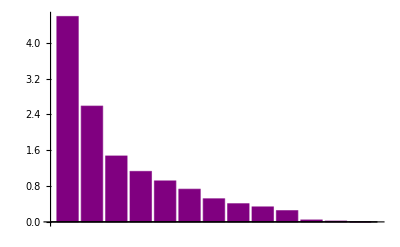

```mathematica
BarChart[varianceOfEachColumn1,ChartStyle->Purple]
```

```mathematica
(*the following function tells us how much of the total variance is accounted for after adding in each principal component. Like the authors, we find the first four principal components explain ~75% of the variance, and five principal components explain ~82%. So we agree that a five-variable regression function might be able to reliably predict the outcome...*)
```

```mathematica
cumulativeVariance1=Accumulate[varianceOfEachColumn1/Total@varianceOfEachColumn1]
```

{0.352978,0.551977,0.665276,0.752026,0.822506,0.878724,0.918507,0.949825,0.975666,0.99508,0.998454,1.,1.}

```mathematica
(*to overlay the two graphs like in the paper, we find we have to reduce the heights of the barchart columns. Anyway, the point is made:*)
```

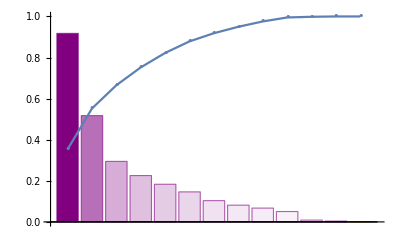

```mathematica
Show[{BarChart[1/5varianceOfEachColumn1,ColorFunction ->Function[{height},Opacity[height]],ChartStyle->Purple],ListPlot[cumulativeVariance1,Joined->True,PlotMarkers->"•"]},PlotRange->All]
```

This could be used to compute optimized variables but the practical application of that would be unwieldy - we don’t want to have to compute all the original input descriptors every time we want to predict the activity of a new compound.

#### Normalized

```mathematica
PCADataN=LogNormedFinalT[[All,1;;-2]]
```

(2.95818 | 2.77306 | 2.77439 | 2.76844 | 2.68039 | 2.77335 | 2.7201 | 2.77259 | 2.79103 | 2.77379 | 2.77699 | 2.78753 | 3.27407
2.80734 | 2.77093 | 2.77151 | 2.76563 | 2.67864 | 2.74875 | 2.74301 | 2.77268 | 2.78556 | 2.77399 | 2.78522 | 2.77335 | 3.27354
2.77289 | 2.76755 | 2.76698 | 2.7661 | 2.75355 | 2.73341 | 2.74071 | 2.77303 | 2.77615 | 2.77251 | 2.76994 | 2.76854 | 3.32938
2.77635 | 2.76749 | 2.76707 | 2.76603 | 2.7511 | 2.7344 | 2.74071 | 2.77277 | 2.78027 | 2.77242 | 2.76994 | 2.76854 | 3.41383
2.76942 | 2.76785 | 2.76676 | 2.76589 | 2.75355 | 2.73103 | 2.74097 | 2.77285 | 2.772 | 2.77259 | 2.77047 | 2.76924 | 3.23713
2.81068 | 2.7719 | 2.76415 | 2.76359 | 2.75566 | 2.75874 | 2.66772 | 2.77303 | 2.78964 | 2.77375 | 2.78278 | 2.77276 | 3.32654
2.96842 | 2.77306 | 2.77444 | 2.76849 | 2.68039 | 2.77391 | 2.7201 | 2.77277 | 2.78694 | 2.77412 | 2.7798 | 2.79007 | 3.21813
2.77979 | 2.76747 | 2.76694 | 2.76608 | 2.75387 | 2.73373 | 2.73969 | 2.77312 | 2.78438 | 2.7723 | 2.76994 | 2.76742 | 3.42585
2.80399 | 2.7709 | 2.7718 | 2.76603 | 2.68074 | 2.75113 | 2.67292 | 2.77259 | 2.78145 | 2.7742 | 2.78609 | 2.77452 | 3.17573
2.80399 | 2.7698 | 2.77037 | 2.76538 | 2.69207 | 2.78835 | 2.64861 | 2.77312 | 2.78145 | 2.77428 | 2.78801 | 2.77452 | 3.14013
2.77605 | 2.7684 | 2.7678 | 2.76901 | 2.78593 | 2.77173 | 2.79603 | 2.77312 | 2.77673 | 2.77242 | 2.77064 | 2.77148 | 3.06686
2.76942 | 2.76816 | 2.76693 | 2.76609 | 2.75436 | 2.73521 | 2.74046 | 2.77338 | 2.772 | 2.77271 | 2.77171 | 2.76936 | 3.27653
2.80734 | 2.7712 | 2.77044 | 2.7654 | 2.69137 | 2.78963 | 2.64833 | 2.77259 | 2.78556 | 2.77408 | 2.78696 | 2.77394 | 3.24132
2.76595 | 2.78138 | 2.76827 | 2.76768 | 2.75939 | 2.74117 | 2.7425 | 2.77321 | 2.76784 | 2.7728 | 2.77241 | 2.77018 | 3.17902
2.78252 | 2.7705 | 2.77062 | 2.77091 | 2.77514 | 2.73469 | 2.77752 | 2.77312 | 2.78084 | 2.77379 | 2.78679 | 2.77942 | 3.12001
2.77949 | 2.76817 | 2.76748 | 2.76853 | 2.78324 | 2.77319 | 2.79699 | 2.77259 | 2.78085 | 2.7723 | 2.77064 | 2.77065 | 3.17534
2.80063 | 2.77236 | 2.77146 | 2.76645 | 2.69293 | 2.79526 | 2.64749 | 2.77268 | 2.77733 | 2.77457 | 2.7894 | 2.77569 | 3.02755
2.77248 | 2.77213 | 2.77112 | 2.77219 | 2.78719 | 2.73958 | 2.79046 | 2.77259 | 2.77199 | 2.7742 | 2.79009 | 2.77889 | 3.13124
2.77949 | 2.77213 | 2.77239 | 2.77256 | 2.77498 | 2.76942 | 2.77555 | 2.77312 | 2.78085 | 2.7723 | 2.77064 | 2.77065 | 3.1049
2.77248 | 2.76817 | 2.76629 | 2.76529 | 2.7511 | 2.73889 | 2.79046 | 2.7733 | 2.77199 | 2.7742 | 2.79009 | 2.77889 | 3.13124
2.78292 | 2.7691 | 2.76737 | 2.7685 | 2.78435 | 2.77401 | 2.79675 | 2.77312 | 2.78496 | 2.77222 | 2.77047 | 2.76995 | 3.27319
2.77605 | 2.77213 | 2.77239 | 2.77253 | 2.77451 | 2.77036 | 2.76565 | 2.77321 | 2.77673 | 2.77246 | 2.77224 | 2.77159 | 3.0383
2.78604 | 2.77306 | 2.77462 | 2.77309 | 2.75094 | 2.73451 | 2.77653 | 2.77321 | 2.78554 | 2.77226 | 2.77011 | 2.77271 | 2.8883
2.77949 | 2.77143 | 2.77168 | 2.77171 | 2.77227 | 2.7685 | 2.7753 | 2.77321 | 2.78085 | 2.77238 | 2.77206 | 2.77077 | 1.86137
2.80399 | 2.77096 | 2.77232 | 2.76786 | 2.70292 | 2.78648 | 2.78242 | 2.77303 | 2.78145 | 2.77428 | 2.78801 | 2.77452 | 3.03518
2.80399 | 2.77073 | 2.77311 | 2.76819 | 2.69604 | 2.78251 | 2.78144 | 2.77268 | 2.78145 | 2.77428 | 2.78801 | 2.77452 | 2.33552
2.80063 | 2.77259 | 2.77274 | 2.76808 | 2.69966 | 2.78819 | 2.78242 | 2.77215 | 2.77733 | 2.77457 | 2.7894 | 2.77569 | 2.90931
2.78252 | 2.77003 | 2.76985 | 2.7692 | 2.76004 | 2.7169 | 2.77997 | 2.77215 | 2.78084 | 2.77379 | 2.78679 | 2.77942 | 3.04541
2.80399 | 2.77026 | 2.77128 | 2.76642 | 2.69518 | 2.79606 | 2.64665 | 2.77241 | 2.78145 | 2.77428 | 2.78801 | 2.77452 | 3.14013
2.80734 | 2.77003 | 2.7701 | 2.76524 | 2.69397 | 2.78885 | 2.64777 | 2.77312 | 2.78556 | 2.77408 | 2.78696 | 2.77394 | 3.24132
2.76595 | 2.77026 | 2.76942 | 2.77101 | 2.79331 | 2.75982 | 2.803 | 2.77312 | 2.76784 | 2.77263 | 2.77135 | 2.77001 | 2.21006
2.74898 | 2.77676 | 2.77765 | 2.77708 | 2.76923 | 2.74014 | 2.75414 | 2.77259 | 2.75407 | 2.77317 | 2.77224 | 2.765 | 3.23566
2.81068 | 2.77003 | 2.77019 | 2.76527 | 2.69293 | 2.78931 | 2.64861 | 2.77303 | 2.78964 | 2.77391 | 2.78609 | 2.77276 | 3.3332
2.79612 | 2.7719 | 2.77335 | 2.77 | 2.72143 | 2.77594 | 2.77604 | 2.77303 | 2.7989 | 2.77441 | 2.78033 | 2.77411 | 3.33469
2.77248 | 2.77167 | 2.77038 | 2.77214 | 2.79675 | 2.73615 | 2.77555 | 2.77312 | 2.77199 | 2.7742 | 2.79009 | 2.77889 | 3.13124
2.76235 | 2.77167 | 2.76998 | 2.76929 | 2.75939 | 2.74681 | 2.79119 | 2.77268 | 2.76306 | 2.77478 | 2.79459 | 2.7782 | 3.13286
2.78292 | 2.7712 | 2.77159 | 2.77167 | 2.77259 | 2.76758 | 2.77555 | 2.77312 | 2.78496 | 2.77226 | 2.77188 | 2.77001 | 3.14696
2.80734 | 2.77003 | 2.76946 | 2.76855 | 2.75566 | 2.7696 | 2.78413 | 2.77294 | 2.78556 | 2.77408 | 2.78696 | 2.77394 | 3.14696
2.80734 | 2.7712 | 2.7727 | 2.76784 | 2.69656 | 2.78323 | 2.78046 | 2.77285 | 2.78556 | 2.77408 | 2.78696 | 2.77394 | 3.14696
2.77604 | 2.77259 | 2.7726 | 2.77257 | 2.77211 | 2.77128 | 2.77061 | 2.77365 | 2.77673 | 2.77242 | 2.77064 | 2.77148 | 2.98803
2.77949 | 2.77096 | 2.77131 | 2.77132 | 2.77147 | 2.76821 | 2.77432 | 2.77312 | 2.78085 | 2.77238 | 2.77206 | 2.77077 | 3.04075
2.77604 | 2.7719 | 2.77211 | 2.77214 | 2.77243 | 2.77325 | 2.7716 | 2.77312 | 2.77673 | 2.77246 | 2.77224 | 2.77159 | 2.91563
2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259
2.77259 | 2.77376 | 2.7748 | 2.77357 | 2.75599 | 2.73776 | 2.78535 | 2.77285 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | -0.393904
2.76594 | 2.77236 | 2.77169 | 2.7719 | 2.77482 | 2.78172 | 2.78608 | 2.77347 | 2.76784 | 2.77263 | 2.77135 | 2.77001 | 2.83458
2.76245 | 2.77236 | 2.77168 | 2.77189 | 2.77498 | 2.7827 | 2.78584 | 2.77312 | 2.76367 | 2.77284 | 2.77365 | 2.77106 | 2.74638)

```mathematica
PrincipalComponentsN=PrincipalComponents[PCADataN,Method->"Correlation"];
```

```mathematica
varianceOfEachColumn2=Variance/@Transpose@PrincipalComponentsN
```

{4.58526,2.48367,1.47643,1.10914,0.831359,0.771299,0.664661,0.417661,0.335238,0.25629,0.0483507,0.0206042,0.0000287514}

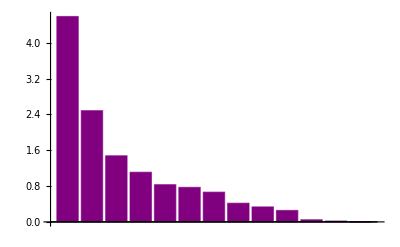

```mathematica
BarChart[varianceOfEachColumn2,ChartStyle->Purple]
```

```mathematica
cumulativeVariance2=Accumulate[varianceOfEachColumn2/Total@varianceOfEachColumn2]
```

{0.352712,0.543764,0.657336,0.742654,0.806605,0.865936,0.917064,0.949191,0.974979,0.994694,0.998413,0.999998,1.}

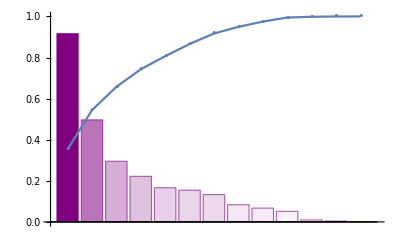

```mathematica
Show[{BarChart[1/5varianceOfEachColumn2,ColorFunction ->Function[{height},Opacity[height]],ChartStyle->Purple],ListPlot[cumulativeVariance2,Joined->True,PlotMarkers->"•"]},PlotRange->All]
```

### Correlation Matrix

The following matrix is a table of Pearson’s correlation coefficients (r values) between each chemical measurement.
High inter-correlation between a pair of characteristics can distort a linear regression analysis, so the authors decided to avoid any pair of characteristics with an absolute value of r greater than 0.8. Only refractive index (n) and surface tension (γ) had such a high inter-correlation; refractive index was therefore left out of the subsequent regression analysis.
Actual formula for correlation coefficient: Correl(X,Y) = [Sum((x-xbar)(y-ybar))]/[SqRt[(Sum(x-xbar)^2)(Sum(y-ybar)^2)]] where xbar and ybar are the averages of the data set for the respective measurements.

```mathematica
Correlation[ActualData]
```

(1. | -0.445075 | -0.264673 | 0.37217 | -0.577815 | -0.333557 | -0.259118 | -0.352955 | 0.196377 | 0.342209 | 0.0539286 | -0.0293615 | 0.199581 | 0.531941
-0.445075 | 1. | -0.0838851 | 0.271229 | 0.258482 | 0.606635 | -0.294584 | 0.33373 | -0.251888 | -0.526888 | -0.351307 | -0.194399 | -0.74975 | -0.202031
-0.264673 | -0.0838851 | 1. | -0.555216 | 0.460072 | -0.00474525 | 0.0570004 | 0.0222463 | 0.0328363 | -0.279507 | 0.0631735 | -0.0262394 | 0.0985546 | -0.246192
0.37217 | 0.271229 | -0.555216 | 1. | -0.633469 | 0.25258 | -0.269334 | -0.0991034 | -0.208526 | 0.0429598 | -0.150405 | -0.0484502 | -0.239614 | 0.395812
-0.577815 | 0.258482 | 0.460072 | -0.633469 | 1. | 0.588676 | -0.120574 | 0.605684 | -0.14666 | -0.430435 | -0.396205 | -0.383033 | -0.126844 | -0.509443
-0.333557 | 0.606635 | -0.00474525 | 0.25258 | 0.588676 | 1. | -0.432335 | 0.653866 | -0.401401 | -0.493919 | -0.652339 | -0.52948 | -0.408954 | -0.223622
-0.259118 | -0.294584 | 0.0570004 | -0.269334 | -0.120574 | -0.432335 | 1. | -0.307771 | 0.0261029 | 0.313594 | 0.250516 | 0.201145 | 0.0827052 | -0.11172
-0.352955 | 0.33373 | 0.0222463 | -0.0991034 | 0.605684 | 0.653866 | -0.307771 | 1. | -0.167066 | -0.325735 | -0.370674 | -0.309641 | -0.110675 | -0.392581
0.196377 | -0.251888 | 0.0328363 | -0.208526 | -0.14666 | -0.401401 | 0.0261029 | -0.167066 | 1. | 0.0568898 | 0.467254 | 0.426957 | 0.334716 | 0.0524229
0.342209 | -0.526888 | -0.279507 | 0.0429598 | -0.430435 | -0.493919 | 0.313594 | -0.325735 | 0.0568898 | 1. | 0.198254 | 0.164145 | 0.290585 | 0.323211
0.0539286 | -0.351307 | 0.0631735 | -0.150405 | -0.396205 | -0.652339 | 0.250516 | -0.370674 | 0.467254 | 0.198254 | 1. | 0.951168 | 0.627186 | 0.176771
-0.0293615 | -0.194399 | -0.0262394 | -0.0484502 | -0.383033 | -0.52948 | 0.201145 | -0.309641 | 0.426957 | 0.164145 | 0.951168 | 1. | 0.578043 | 0.116499
0.199581 | -0.74975 | 0.0985546 | -0.239614 | -0.126844 | -0.408954 | 0.0827052 | -0.110675 | 0.334716 | 0.290585 | 0.627186 | 0.578043 | 1. | 0.0434568
0.531941 | -0.202031 | -0.246192 | 0.395812 | -0.509443 | -0.223622 | -0.11172 | -0.392581 | 0.0524229 | 0.323211 | 0.176771 | 0.116499 | 0.0434568 | 1.)

We find again that n and γ are too highly correlated (R=0.951). Like the authors, we drop n.

```mathematica
(*drop -4th column*)
goodData1=ReplacePart[ActualData,{_,-4}->Nothing]
```

(2.72 | -82328.7 | 7.374 | -5.682 | 5.522 | -0.16 | 3.242 | 0.046 | -0.707 | 274.154 | 37.9 | 1.324 | 2.455
1.96 | -30241. | 7.125 | -5.428 | 5.258 | -0.17 | 1.996 | 0.135 | -0.708 | 255.376 | 42.6 | 1.08 | 2.452
2.02 | -19406.4 | 6.731 | -5.029 | 5.302 | 0.273 | 1.234 | 0.126 | -0.712 | 223.311 | 33.9 | 0.998 | 2.778
1.95 | -20476.1 | 6.724 | -5.037 | 5.295 | 0.258 | 1.283 | 0.126 | -0.709 | 237.338 | 33.9 | 0.998 | 3.307
1.9 | -18336.7 | 6.765 | -5.009 | 5.282 | 0.273 | 1.117 | 0.127 | -0.71 | 209.285 | 34.2 | 1.01 | 2.249
1.71 | -31310.7 | 7.238 | -4.78 | 5.066 | 0.286 | 2.498 | -0.15 | -0.712 | 269.403 | 41.2 | 1.07 | 2.761
1.69 | -86156.7 | 7.374 | -5.687 | 5.527 | -0.16 | 3.271 | 0.046 | -0.709 | 260.128 | 39.5 | 1.368 | 2.146
1.68 | -21545.9 | 6.721 | -5.025 | 5.3 | 0.275 | 1.25 | 0.122 | -0.713 | 251.365 | 33.9 | 0.979 | 3.386
1.66 | -29171.2 | 7.121 | -5.453 | 5.295 | -0.158 | 2.115 | -0.131 | -0.707 | 241.35 | 43.1 | 1.1 | 1.923
1.36 | -29171. | 6.993 | -5.327 | 5.234 | -0.093 | 4.017 | -0.219 | -0.713 | 241.35 | 44.2 | 1.1 | 1.743
1.33 | -20382.8 | 6.83 | -5.101 | 5.576 | 0.475 | 3.159 | 0.349 | -0.713 | 225.284 | 34.3 | 1.048 | 1.392
1.25 | -18336.6 | 6.802 | -5.024 | 5.301 | 0.278 | 1.323 | 0.125 | -0.716 | 209.285 | 34.9 | 1.012 | 2.469
1.29 | -30240.9 | 7.156 | -5.333 | 5.236 | -0.097 | 4.084 | -0.22 | -0.707 | 255.376 | 43.6 | 1.09 | 2.272
1.27 | -17266.8 | 8.353 | -5.142 | 5.451 | 0.309 | 1.618 | 0.133 | -0.714 | 195.258 | 35.3 | 1.026 | 1.94
1.14 | -22396.4 | 7.075 | -5.349 | 5.755 | 0.407 | 1.297 | 0.273 | -0.713 | 239.268 | 43.5 | 1.184 | 1.644
1.36 | -21452.6 | 6.803 | -5.073 | 5.531 | 0.458 | 3.234 | 0.353 | -0.707 | 239.311 | 34.3 | 1.034 | 1.921
1.11 | -28101.4 | 7.292 | -5.423 | 5.335 | -0.088 | 4.378 | -0.223 | -0.708 | 227.323 | 45. | 1.12 | 1.214
1. | -19280.5 | 7.265 | -5.393 | 5.876 | 0.483 | 1.539 | 0.326 | -0.707 | 209.242 | 45.4 | 1.175 | 1.699
1.05 | -21452.6 | 7.265 | -5.505 | 5.911 | 0.406 | 3.041 | 0.265 | -0.713 | 239.311 | 34.3 | 1.034 | 1.571
1. | -19280.5 | 6.803 | -4.968 | 5.226 | 0.258 | 1.505 | 0.326 | -0.715 | 209.242 | 45.4 | 1.175 | 1.699
1.38 | -22522.4 | 6.911 | -5.063 | 5.528 | 0.465 | 3.276 | 0.352 | -0.713 | 253.337 | 34.2 | 1.022 | 2.45
0.87 | -20382.8 | 7.265 | -5.505 | 5.908 | 0.403 | 3.089 | 0.225 | -0.714 | 225.284 | 35.2 | 1.05 | 1.262
0.86 | -23498.6 | 7.374 | -5.703 | 5.961 | 0.257 | 1.288 | 0.269 | -0.714 | 255.31 | 34. | 1.069 | 0.637
0.83 | -21452.5 | 7.183 | -5.443 | 5.831 | 0.389 | 2.994 | 0.264 | -0.714 | 239.311 | 35.1 | 1.036 | -1.842
0.84 | -29171. | 7.129 | -5.499 | 5.468 | -0.03 | 3.92 | 0.293 | -0.712 | 241.35 | 44.2 | 1.1 | 1.248
0.84 | -29171. | 7.102 | -5.569 | 5.499 | -0.07 | 3.714 | 0.289 | -0.708 | 241.35 | 44.2 | 1.1 | -1.003
0.81 | -28101.4 | 7.319 | -5.536 | 5.488 | -0.049 | 4.009 | 0.293 | -0.702 | 227.323 | 45. | 1.12 | 0.719
0.76 | -22396.4 | 7.02 | -5.281 | 5.594 | 0.313 | 0.427 | 0.283 | -0.702 | 239.268 | 43.5 | 1.184 | 1.294
0.66 | -29171. | 7.047 | -5.407 | 5.332 | -0.075 | 4.42 | -0.226 | -0.705 | 241.35 | 44.2 | 1.1 | 1.743
0.68 | -30240.9 | 7.02 | -5.303 | 5.221 | -0.082 | 4.043 | -0.222 | -0.713 | 255.376 | 43.6 | 1.09 | 2.272
0.67 | -17266.9 | 7.047 | -5.243 | 5.765 | 0.522 | 2.553 | 0.378 | -0.713 | 195.258 | 34.7 | 1.023 | -1.265
0.59 | -12104.5 | 7.809 | -5.971 | 6.34 | 0.37 | 1.567 | 0.179 | -0.707 | 149.233 | 35.2 | 0.938 | 2.241
0.58 | -31310.5 | 7.02 | -5.311 | 5.224 | -0.088 | 4.067 | -0.219 | -0.712 | 269.403 | 43.1 | 1.07 | 2.801
0.46 | -26669.7 | 7.238 | -5.59 | 5.669 | 0.079 | 3.375 | 0.267 | -0.712 | 301.38 | 39.8 | 1.093 | 2.81
0.43 | -19280.5 | 7.211 | -5.328 | 5.872 | 0.544 | 1.369 | 0.265 | -0.713 | 209.242 | 45.4 | 1.175 | 1.699
0.41 | -16164.5 | 7.211 | -5.293 | 5.602 | 0.309 | 1.899 | 0.329 | -0.708 | 179.216 | 48. | 1.163 | 1.707
0.38 | -22522.2 | 7.156 | -5.435 | 5.827 | 0.391 | 2.947 | 0.265 | -0.713 | 253.337 | 35. | 1.023 | 1.777
0.38 | -30240.9 | 7.02 | -5.247 | 5.533 | 0.286 | 3.05 | 0.3 | -0.711 | 255.376 | 43.6 | 1.09 | 1.777
0.38 | -30240.9 | 7.156 | -5.533 | 5.466 | -0.067 | 3.751 | 0.285 | -0.71 | 255.376 | 43.6 | 1.09 | 1.777
0.33 | -20382.8 | 7.319 | -5.524 | 5.912 | 0.388 | 3.136 | 0.245 | -0.719 | 225.284 | 34.3 | 1.048 | 1.042
0.23 | -21452.6 | 7.129 | -5.41 | 5.794 | 0.384 | 2.979 | 0.26 | -0.713 | 239.311 | 35.1 | 1.036 | 1.273
0.03 | -20382.7 | 7.238 | -5.481 | 5.872 | 0.39 | 3.237 | 0.249 | -0.713 | 225.284 | 35.2 | 1.05 | 0.744
0. | -19312.9 | 7.319 | -5.523 | 5.914 | 0.391 | 3.203 | 0.253 | -0.707 | 211.258 | 35.4 | 1.067 | 0.215
-0.03 | -19312.8 | 7.456 | -5.719 | 6.007 | 0.288 | 1.449 | 0.305 | -0.71 | 211.258 | 35.4 | 1.067 | -3.08
-0.06 | -17266.8 | 7.292 | -5.444 | 5.849 | 0.405 | 3.673 | 0.308 | -0.717 | 195.258 | 34.7 | 1.023 | 0.435
-0.67 | -16196.9 | 7.292 | -5.443 | 5.848 | 0.406 | 3.724 | 0.307 | -0.713 | 181.232 | 36. | 1.041 | 0.126)

```mathematica
GoodDataNormalized=ReplacePart[LogNormedFinalT,{_,-5}->Nothing]
```

(2.95818 | 2.77306 | 2.77439 | 2.76844 | 2.68039 | 2.77335 | 2.7201 | 2.77259 | 2.79103 | 2.77699 | 2.78753 | 3.27407 | 2.72
2.80734 | 2.77093 | 2.77151 | 2.76563 | 2.67864 | 2.74875 | 2.74301 | 2.77268 | 2.78556 | 2.78522 | 2.77335 | 3.27354 | 1.96
2.77289 | 2.76755 | 2.76698 | 2.7661 | 2.75355 | 2.73341 | 2.74071 | 2.77303 | 2.77615 | 2.76994 | 2.76854 | 3.32938 | 2.02
2.77635 | 2.76749 | 2.76707 | 2.76603 | 2.7511 | 2.7344 | 2.74071 | 2.77277 | 2.78027 | 2.76994 | 2.76854 | 3.41383 | 1.95
2.76942 | 2.76785 | 2.76676 | 2.76589 | 2.75355 | 2.73103 | 2.74097 | 2.77285 | 2.772 | 2.77047 | 2.76924 | 3.23713 | 1.9
2.81068 | 2.7719 | 2.76415 | 2.76359 | 2.75566 | 2.75874 | 2.66772 | 2.77303 | 2.78964 | 2.78278 | 2.77276 | 3.32654 | 1.71
2.96842 | 2.77306 | 2.77444 | 2.76849 | 2.68039 | 2.77391 | 2.7201 | 2.77277 | 2.78694 | 2.7798 | 2.79007 | 3.21813 | 1.69
2.77979 | 2.76747 | 2.76694 | 2.76608 | 2.75387 | 2.73373 | 2.73969 | 2.77312 | 2.78438 | 2.76994 | 2.76742 | 3.42585 | 1.68
2.80399 | 2.7709 | 2.7718 | 2.76603 | 2.68074 | 2.75113 | 2.67292 | 2.77259 | 2.78145 | 2.78609 | 2.77452 | 3.17573 | 1.66
2.80399 | 2.7698 | 2.77037 | 2.76538 | 2.69207 | 2.78835 | 2.64861 | 2.77312 | 2.78145 | 2.78801 | 2.77452 | 3.14013 | 1.36
2.77605 | 2.7684 | 2.7678 | 2.76901 | 2.78593 | 2.77173 | 2.79603 | 2.77312 | 2.77673 | 2.77064 | 2.77148 | 3.06686 | 1.33
2.76942 | 2.76816 | 2.76693 | 2.76609 | 2.75436 | 2.73521 | 2.74046 | 2.77338 | 2.772 | 2.77171 | 2.76936 | 3.27653 | 1.25
2.80734 | 2.7712 | 2.77044 | 2.7654 | 2.69137 | 2.78963 | 2.64833 | 2.77259 | 2.78556 | 2.78696 | 2.77394 | 3.24132 | 1.29
2.76595 | 2.78138 | 2.76827 | 2.76768 | 2.75939 | 2.74117 | 2.7425 | 2.77321 | 2.76784 | 2.77241 | 2.77018 | 3.17902 | 1.27
2.78252 | 2.7705 | 2.77062 | 2.77091 | 2.77514 | 2.73469 | 2.77752 | 2.77312 | 2.78084 | 2.78679 | 2.77942 | 3.12001 | 1.14
2.77949 | 2.76817 | 2.76748 | 2.76853 | 2.78324 | 2.77319 | 2.79699 | 2.77259 | 2.78085 | 2.77064 | 2.77065 | 3.17534 | 1.36
2.80063 | 2.77236 | 2.77146 | 2.76645 | 2.69293 | 2.79526 | 2.64749 | 2.77268 | 2.77733 | 2.7894 | 2.77569 | 3.02755 | 1.11
2.77248 | 2.77213 | 2.77112 | 2.77219 | 2.78719 | 2.73958 | 2.79046 | 2.77259 | 2.77199 | 2.79009 | 2.77889 | 3.13124 | 1.
2.77949 | 2.77213 | 2.77239 | 2.77256 | 2.77498 | 2.76942 | 2.77555 | 2.77312 | 2.78085 | 2.77064 | 2.77065 | 3.1049 | 1.05
2.77248 | 2.76817 | 2.76629 | 2.76529 | 2.7511 | 2.73889 | 2.79046 | 2.7733 | 2.77199 | 2.79009 | 2.77889 | 3.13124 | 1.
2.78292 | 2.7691 | 2.76737 | 2.7685 | 2.78435 | 2.77401 | 2.79675 | 2.77312 | 2.78496 | 2.77047 | 2.76995 | 3.27319 | 1.38
2.77605 | 2.77213 | 2.77239 | 2.77253 | 2.77451 | 2.77036 | 2.76565 | 2.77321 | 2.77673 | 2.77224 | 2.77159 | 3.0383 | 0.87
2.78604 | 2.77306 | 2.77462 | 2.77309 | 2.75094 | 2.73451 | 2.77653 | 2.77321 | 2.78554 | 2.77011 | 2.77271 | 2.8883 | 0.86
2.77949 | 2.77143 | 2.77168 | 2.77171 | 2.77227 | 2.7685 | 2.7753 | 2.77321 | 2.78085 | 2.77206 | 2.77077 | 1.86137 | 0.83
2.80399 | 2.77096 | 2.77232 | 2.76786 | 2.70292 | 2.78648 | 2.78242 | 2.77303 | 2.78145 | 2.78801 | 2.77452 | 3.03518 | 0.84
2.80399 | 2.77073 | 2.77311 | 2.76819 | 2.69604 | 2.78251 | 2.78144 | 2.77268 | 2.78145 | 2.78801 | 2.77452 | 2.33552 | 0.84
2.80063 | 2.77259 | 2.77274 | 2.76808 | 2.69966 | 2.78819 | 2.78242 | 2.77215 | 2.77733 | 2.7894 | 2.77569 | 2.90931 | 0.81
2.78252 | 2.77003 | 2.76985 | 2.7692 | 2.76004 | 2.7169 | 2.77997 | 2.77215 | 2.78084 | 2.78679 | 2.77942 | 3.04541 | 0.76
2.80399 | 2.77026 | 2.77128 | 2.76642 | 2.69518 | 2.79606 | 2.64665 | 2.77241 | 2.78145 | 2.78801 | 2.77452 | 3.14013 | 0.66
2.80734 | 2.77003 | 2.7701 | 2.76524 | 2.69397 | 2.78885 | 2.64777 | 2.77312 | 2.78556 | 2.78696 | 2.77394 | 3.24132 | 0.68
2.76595 | 2.77026 | 2.76942 | 2.77101 | 2.79331 | 2.75982 | 2.803 | 2.77312 | 2.76784 | 2.77135 | 2.77001 | 2.21006 | 0.67
2.74898 | 2.77676 | 2.77765 | 2.77708 | 2.76923 | 2.74014 | 2.75414 | 2.77259 | 2.75407 | 2.77224 | 2.765 | 3.23566 | 0.59
2.81068 | 2.77003 | 2.77019 | 2.76527 | 2.69293 | 2.78931 | 2.64861 | 2.77303 | 2.78964 | 2.78609 | 2.77276 | 3.3332 | 0.58
2.79612 | 2.7719 | 2.77335 | 2.77 | 2.72143 | 2.77594 | 2.77604 | 2.77303 | 2.7989 | 2.78033 | 2.77411 | 3.33469 | 0.46
2.77248 | 2.77167 | 2.77038 | 2.77214 | 2.79675 | 2.73615 | 2.77555 | 2.77312 | 2.77199 | 2.79009 | 2.77889 | 3.13124 | 0.43
2.76235 | 2.77167 | 2.76998 | 2.76929 | 2.75939 | 2.74681 | 2.79119 | 2.77268 | 2.76306 | 2.79459 | 2.7782 | 3.13286 | 0.41
2.78292 | 2.7712 | 2.77159 | 2.77167 | 2.77259 | 2.76758 | 2.77555 | 2.77312 | 2.78496 | 2.77188 | 2.77001 | 3.14696 | 0.38
2.80734 | 2.77003 | 2.76946 | 2.76855 | 2.75566 | 2.7696 | 2.78413 | 2.77294 | 2.78556 | 2.78696 | 2.77394 | 3.14696 | 0.38
2.80734 | 2.7712 | 2.7727 | 2.76784 | 2.69656 | 2.78323 | 2.78046 | 2.77285 | 2.78556 | 2.78696 | 2.77394 | 3.14696 | 0.38
2.77604 | 2.77259 | 2.7726 | 2.77257 | 2.77211 | 2.77128 | 2.77061 | 2.77365 | 2.77673 | 2.77064 | 2.77148 | 2.98803 | 0.33
2.77949 | 2.77096 | 2.77131 | 2.77132 | 2.77147 | 2.76821 | 2.77432 | 2.77312 | 2.78085 | 2.77206 | 2.77077 | 3.04075 | 0.23
2.77604 | 2.7719 | 2.77211 | 2.77214 | 2.77243 | 2.77325 | 2.7716 | 2.77312 | 2.77673 | 2.77224 | 2.77159 | 2.91563 | 0.03
2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 0.
2.77259 | 2.77376 | 2.7748 | 2.77357 | 2.75599 | 2.73776 | 2.78535 | 2.77285 | 2.77259 | 2.77259 | 2.77259 | -0.393904 | -0.03
2.76594 | 2.77236 | 2.77169 | 2.7719 | 2.77482 | 2.78172 | 2.78608 | 2.77347 | 2.76784 | 2.77135 | 2.77001 | 2.83458 | -0.06
2.76245 | 2.77236 | 2.77168 | 2.77189 | 2.77498 | 2.7827 | 2.78584 | 2.77312 | 2.76367 | 2.77365 | 2.77106 | 2.74638 | -0.67)

### Multiple Linear Regression Analysis

The purpose of the following analysis is to recapitulate the linear models in the Aouidate, et al paper.

```mathematica
(*map applies an operation to every row. Here we want to move the first column (which contains the response variable logUM) to the end*)
reformatted12=Map[Flatten@{#[[2;;-1]],#[[1]]}&,goodData1];
```

```mathematica
Dimensions[reformatted12]
```

{46,13}

```mathematica
(*Now I will first try a linear model with all 12 descriptors*)
```

```mathematica
model12=LinearModelFit[reformatted12,Table[x[i],{i,1,12}],Table[x[i],{i,1,12}]]
```

FittedModel[«15»+0.00121584 x[9]-0.0410994 x[10]-0.55746 x[11]+0.0802493 x[12]]

```mathematica
model12["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
model12["RSquared"]
```

0.722616

```mathematica
(*Fitting Normalized Data!*)
```

```mathematica
model13=LinearModelFit[GoodDataNormalized,Table[x[i],{i,1,12}],Table[x[i],{i,1,12}]]
```

FittedModel[1157.82+7.15801 x[1]+4.44003 x[2]-4709.14 x[3]+«9»+2.85123 x[9]-22.1644 x[10]-24.6087 x[11]+0.172456 x[12]]

```mathematica
model13["RSquared"]
```

0.758252

### Linear Regression with the Five Variables Aouidate, et al Recommend

```mathematica
recommendedData1=reformatted12[[All,{1,3,5,6,10,-1}]];
```

```mathematica
model5=LinearModelFit[recommendedData1,Table[x[i],{i,1,5}],Table[x[i],{i,1,5}]]
```

FittedModel[10.4527-0.0000216893 x[1]+1.39137 x[2]-1.53798 x[3]-0.260324 x[4]-0.040324 x[5]]

```mathematica
model5["BestFitParameters"]
```

{10.4527,-0.0000216893,1.39137,-1.53798,-0.260324,-0.040324}

```mathematica
model5["RSquared"]
```

0.674987

Our linear RSquared is a bit lower than the authors’. That’s interesting.

```mathematica
(*Now with Normalized data*)
```

```mathematica
recommendedData2=GoodDataNormalized[[All,{1,3,5,6,10,-1}]]
```

(2.95818 | 2.77439 | 2.68039 | 2.77335 | 2.77699 | 2.72
2.80734 | 2.77151 | 2.67864 | 2.74875 | 2.78522 | 1.96
2.77289 | 2.76698 | 2.75355 | 2.73341 | 2.76994 | 2.02
2.77635 | 2.76707 | 2.7511 | 2.7344 | 2.76994 | 1.95
2.76942 | 2.76676 | 2.75355 | 2.73103 | 2.77047 | 1.9
2.81068 | 2.76415 | 2.75566 | 2.75874 | 2.78278 | 1.71
2.96842 | 2.77444 | 2.68039 | 2.77391 | 2.7798 | 1.69
2.77979 | 2.76694 | 2.75387 | 2.73373 | 2.76994 | 1.68
2.80399 | 2.7718 | 2.68074 | 2.75113 | 2.78609 | 1.66
2.80399 | 2.77037 | 2.69207 | 2.78835 | 2.78801 | 1.36
2.77605 | 2.7678 | 2.78593 | 2.77173 | 2.77064 | 1.33
2.76942 | 2.76693 | 2.75436 | 2.73521 | 2.77171 | 1.25
2.80734 | 2.77044 | 2.69137 | 2.78963 | 2.78696 | 1.29
2.76595 | 2.76827 | 2.75939 | 2.74117 | 2.77241 | 1.27
2.78252 | 2.77062 | 2.77514 | 2.73469 | 2.78679 | 1.14
2.77949 | 2.76748 | 2.78324 | 2.77319 | 2.77064 | 1.36
2.80063 | 2.77146 | 2.69293 | 2.79526 | 2.7894 | 1.11
2.77248 | 2.77112 | 2.78719 | 2.73958 | 2.79009 | 1.
2.77949 | 2.77239 | 2.77498 | 2.76942 | 2.77064 | 1.05
2.77248 | 2.76629 | 2.7511 | 2.73889 | 2.79009 | 1.
2.78292 | 2.76737 | 2.78435 | 2.77401 | 2.77047 | 1.38
2.77605 | 2.77239 | 2.77451 | 2.77036 | 2.77224 | 0.87
2.78604 | 2.77462 | 2.75094 | 2.73451 | 2.77011 | 0.86
2.77949 | 2.77168 | 2.77227 | 2.7685 | 2.77206 | 0.83
2.80399 | 2.77232 | 2.70292 | 2.78648 | 2.78801 | 0.84
2.80399 | 2.77311 | 2.69604 | 2.78251 | 2.78801 | 0.84
2.80063 | 2.77274 | 2.69966 | 2.78819 | 2.7894 | 0.81
2.78252 | 2.76985 | 2.76004 | 2.7169 | 2.78679 | 0.76
2.80399 | 2.77128 | 2.69518 | 2.79606 | 2.78801 | 0.66
2.80734 | 2.7701 | 2.69397 | 2.78885 | 2.78696 | 0.68
2.76595 | 2.76942 | 2.79331 | 2.75982 | 2.77135 | 0.67
2.74898 | 2.77765 | 2.76923 | 2.74014 | 2.77224 | 0.59
2.81068 | 2.77019 | 2.69293 | 2.78931 | 2.78609 | 0.58
2.79612 | 2.77335 | 2.72143 | 2.77594 | 2.78033 | 0.46
2.77248 | 2.77038 | 2.79675 | 2.73615 | 2.79009 | 0.43
2.76235 | 2.76998 | 2.75939 | 2.74681 | 2.79459 | 0.41
2.78292 | 2.77159 | 2.77259 | 2.76758 | 2.77188 | 0.38
2.80734 | 2.76946 | 2.75566 | 2.7696 | 2.78696 | 0.38
2.80734 | 2.7727 | 2.69656 | 2.78323 | 2.78696 | 0.38
2.77604 | 2.7726 | 2.77211 | 2.77128 | 2.77064 | 0.33
2.77949 | 2.77131 | 2.77147 | 2.76821 | 2.77206 | 0.23
2.77604 | 2.77211 | 2.77243 | 2.77325 | 2.77224 | 0.03
2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 0.
2.77259 | 2.7748 | 2.75599 | 2.73776 | 2.77259 | -0.03
2.76594 | 2.77169 | 2.77482 | 2.78172 | 2.77135 | -0.06
2.76245 | 2.77168 | 2.77498 | 2.7827 | 2.77365 | -0.67)

```mathematica
model6=LinearModelFit[recommendedData2,Table[x[i],{i,1,5}],Table[x[i],{i,1,5}]]
```

FittedModel[446.491+7.38249 x[1]-122.096 x[2]-9.22124 x[3]-13.3467 x[4]-23.6401 x[5]]

```mathematica
model6["RSquared"]
```

0.678029

### Non-Linear Regression

```mathematica
nonlinear5=NonlinearModelFit[
recommendedData1,
a+b x1+c x2+d x3+e x4+f x5+g x1^2+h x2^2+n x3^2+m x4^2+k x5^2,{a,b,c,d,e,f,g,h,n,m,k},
{x1,x2,x3,x4,x5}
]
```

FittedModel[90.3671-0.000091531 x1-6.87724×10^-10 x1^2+22.0414 x2+«19» x2^2-«1»+«18» («2»)^2-0.301465 x4-0.00106867 x4^2-1.37504 x5+0.0165701 x5^2]

```mathematica
nonlinear5["BestFitParameters"]
```

{a→90.3671,b→-0.000091531,c→22.0414,d→-3.77805,e→-0.301465,f→-1.37504,g→-6.87724×10^-10,h→1.94603,n→6.52962,m→-0.00106867,k→0.0165701}

```mathematica
nonlinear5["RSquared"]
```

0.932038

Our non-linear RSquared is fantastic, and higher than the authors’. That’s suspicious and also interesting.

```mathematica
nonlinear6=NonlinearModelFit[
recommendedData2,
a+b x1+c x2+d x3+e x4+f x5+g x1^2+h x2^2+n x3^2+m x4^2+k x5^2,{a,b,c,d,e,f,g,h,n,m,k},
{x1,x2,x3,x4,x5}
]
```

FittedModel[161598.+406.098 x1-69.6159 x1^2-85428.1 x2+15397.4 x2^2-«1»+«18» «1»+21.0258 x4-6.58385 x4^2-30107.5 x5+5408.81 x5^2]

```mathematica
nonlinear6["RSquared"]
```

0.932023

```mathematica
(*Skipping the step below temporarily*)
```

### External Validation

I will randomly select 35 of the 46 compounds to train a similar non-linear model fit, then see how well it does predicting the log(UM)’s of the rest.

```mathematica
TakeDrop[RandomSample[{1,2,3,4,5}],2]
```

{{2,5},{4,1,3}}

```mathematica
(*Magic incantation to split the data: Set a list of two names (training and testing) equal to a function, the output of which is a list of two lists. The two lists are a random sample of the data with the specified length and then the rest of the data*)
```

```mathematica
{training,testing}=TakeDrop[RandomSample[recommendedData1],35];
```

```mathematica
Dimensions[testing]
```

{11,6}

```mathematica
Dimensions[training]
```

{35,6}

```mathematica
nonlinear5and35 = NonlinearModelFit[
training,
a+b x1+c x2+d x3+e x4+f x5+g x1^2+h x2^2+n x3^2+m x4^2+k x5^2,{a,b,c,d,e,f,g,h,n,m,k},
{x1,x2,x3,x4,x5}
]
```

FittedModel[105.955-0.000111238 x1-8.1458×10^-10 x1^2+26.4566 x2+«19» x2^2-«1»+«18» «1»-0.464663 x4+0.0331275 x4^2-1.59004 x5+0.0191646 x5^2]

```mathematica
nonlinear5and35["RSquared"]
```

0.945245

```mathematica
observed=testing[[All,-1]]
```

{0.58,1.27,0.83,0.86,1.,1.25,1.95,1.69,-0.06,0.38,1.}

```mathematica
predicted=Map[
nonlinear5and35["BestFit"]/.Thread[{x1,x2,x3,x4,x5,output}->#]&,
testing
]
```

{1.13911,0.82894,0.426561,1.37547,1.03543,1.4016,1.83253,2.43951,0.047784,0.911016,0.429587}

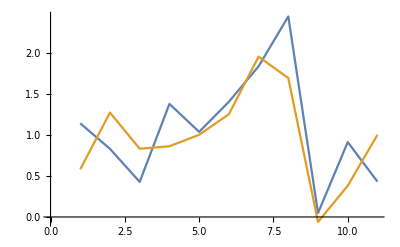

```mathematica
ListLinePlot[{predicted,observed}]
```

```mathematica
combinedData=Transpose[{predicted,observed}]
```

{{1.13911,0.58},{0.82894,1.27},{0.426561,0.83},{1.37547,0.86},{1.03543,1.},{1.4016,1.25},{1.83253,1.95},{2.43951,1.69},{0.047784,-0.06},{0.911016,0.38},{0.429587,1.}}

```mathematica
(*what follows is a scatter plot with observed values on the y axis and predicted on the x*)
```

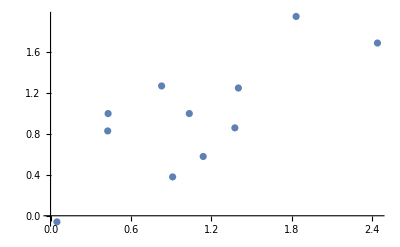

```mathematica
testlistplot=ListPlot@combinedData
```

```mathematica
fit=LinearModelFit[combinedData,x,x]
```

FittedModel[0.297618+0.629972 x]

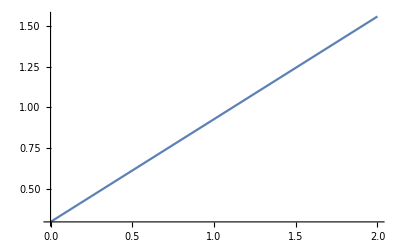

```mathematica
linePlot=Plot[fit["BestFit"],{x,0,2}]
```

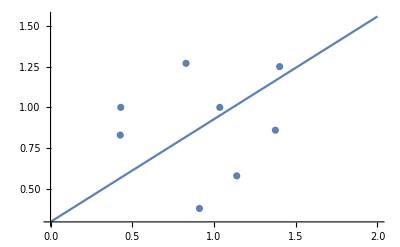

```mathematica
Show[linePlot,testlistplot]
```

```mathematica
(*R-Squared value of the above plot*)
```

```mathematica
fit["RSquared"]
```

0.565422

```mathematica
(*Pearson's correlation coefficient of the resulting list of predicted and observed values*)
```

```mathematica
Correlation[combinedData]
```

{{1.,0.751946},{0.751946,1.}}

Even knowing that predicted and observed vary in the same direction 80% of the time would be useful to chemists in the real world - we usually take qualitative information from these models and use it to optimize structure.

Future goals: Recapitulate the backwards linear regression to validate that the selected five variables really are the best set to predict activity. The authors claim that when they did backwards linear regression from a model with all 12 descriptors (a mix of physicochemical things like logP, MW, etc and electronic descriptors like Ehomo, absolute hardness) the best linear fit was the five variables used above (Etotal, Ehomo, Elumo, absolute hardness and surface tension). We could validate that that’s true by generating the R^2’s of linear fit of all 12c5 = 792 possible combinations.

### “Backwards” Linear Regression

Here by “backwards” regression we mean testing linear model fits from matrices of smaller subsets of the descriptors and the response variable logUM. In this case we will try five-variable design matrices because the PCA analysis indicates five variables may suffice to model this data. From 12 variables, there are 792 different combinations of five. Aouidate, et al claim that the best fit was with the aforementioned five variables of Etotal, Ehomo, Elumo, absolute hardness and surface tension. I want to check/verify that and I also want to know what the runners-up were.

```mathematica
(*What follows is the development of an algorith. Work largely by Dr. Keane*)
```

```mathematica
whichParameters=Subsets[Range[Length@First@reformatted12-1],{5}];
```

```mathematica
Length[whichParameters]
```

792

```mathematica
(*by eye and by showing that the list contains 12c5=792 combos, I think the function above is correct*)
```

```mathematica
whichParameters2=Append[#,-1]&/@whichParameters;
```

```mathematica
Length[whichParameters2]
```

792

```mathematica
parameters=whichParameters2[[1]]
```

{1,2,3,4,5,-1}

```mathematica
(*confirmed, that's the first member of the list*)
```

```mathematica
regressThese=Part[reformatted12,All,parameters];
```

```mathematica
Length[regressThese]
```

46

```mathematica
(*Confirmed that the output of "regressThese" is a list of 46 lists, where each list is the values of the first five descriptors, then logUM, for each compound*)

(*If I understand correctly, what follows is a linear model fit in which the design matrix is the first five columns of regressThese and the response vector is the (-1) column?*)
```

```mathematica
LinearModelFit[regressThese,Table[x[i],{i,1,5}],Table[x[i],{i,1,5}]]["RSquared"]
```

0.488425

```mathematica
(*Assuming everything's written right, that means the first variable set, columns 1-5 {ET IP EHOMO η ELUMO DM} has an R^2 of 0.488425?*)
```

```mathematica
allRSquared=MapIndexed[
Function[
{parameters,index},
regressThese=Part[reformatted12,All,parameters];
First@index->LinearModelFit[regressThese,Table[x[i],{i,1,5}],Table[x[i],{i,1,5}]]["RSquared"]
],
whichParameters2
];
```

```mathematica
(*Here's the most important place to be sure I understand what's going on. Before we defined "parameters" as the first entry of "whichParameters2", but here we are repeating the function for all possible values of "parameters", corresponding to every entry in whichParameters2. We're then taking those values of "parameters" and using them to create the 792 different values of regressThese, each a matrix in the format [design matrix | response vector]. Then we're running a linear model fit for each value of regressThese and spitting out the RSquared value. Right?*)
```

```mathematica
Length[allRSquared]
```

792

```mathematica
(*confirmed the length of the output is 792*)
```

```mathematica
bestFits=TakeLargestBy[allRSquared,Last,UpTo[5]]
```

{239→0.692559,232→0.691919,240→0.689036,233→0.684371,238→0.68246}

```mathematica
(*Below, will find out which sets of variables correspond to the five best RSquared values above. Here's where things get interesting!*)
```

```mathematica
whichParameters2[[{239,232,240,233,238}]]
```

(1 | 4 | 6 | 10 | 12 | -1
1 | 4 | 6 | 8 | 10 | -1
1 | 4 | 6 | 11 | 12 | -1
1 | 4 | 6 | 8 | 11 | -1
1 | 4 | 6 | 10 | 11 | -1)

Analysis:
Yikes, I think I'm getting a different result from the author that' s interesting in a couple ways. Those linear fits are almost identical RSquared' s. 1, 4, and 6 are Etotal, absolute hardness, and dipole moment respectively; 10, 11 and 12 are surface tension, density and logP; 8 is Qmin, the most negative net atomic charge, which is also from DFT but did not factor into the final models in the original paper at all!
I used the Find command to find the entry in the output of the AllRSquared function above, with a RSquared value to match the earlier five-variable linear model fit. It's entry #152. Below, I use the whichParameters2 function to find the column numbers corresponding to that output. Those column numbers indeed match the variables from the five-variable linear model in the Aouidate paper, the same model we recapitulated earlier in this project. That gives me more certainty of the analysis above.
What Madeleine thinks: Absolute hardness (η) is the only DFT descriptor, and (calculated) logP the only physicochemical descriptor, with an absolute value of the Pearson’s correlation coefficient with logUM greater than 0.5, interpreted to mean moving together with logUM more than half the time, so it makes sense that those two descriptors would show up in the best linear model fits. Aouidate, et al were not terribly clear about how they defined “best linear fit” so I went with RSquared for now and noted that the RSquared’s for the top hits above and the model with Aouidate, et al’s recommended descriptors are within 2% of each other. I think an interesting future direction would be to 1) explore what other descriptors I can get out of a DFT structure... HOMO orbital coefficient at an atom involved in a key interaction for a set of compounds of interest?? 2) Repeat this analysis with more biochemically relevant, and possibly empirical, physicochemical descriptors and see if the DFT descriptors still win out/end up being highly represented in the best fit.

#### Normalized

```mathematica
whichParametersNorm=Subsets[Range[Length@First@GoodDataNormalized-1],{5}];
```

```mathematica
Length[whichParametersNorm]
```

792

```mathematica
whichParametersNorm2=Append[#,-1]&/@whichParameters;
```

```mathematica
Length[whichParametersNorm2]
```

792

```mathematica
parameters=whichParametersNorm2[[1]]
```

{1,2,3,4,5,-1}

```mathematica
regressThese2=Part[GoodDataNormalized,All,parameters]
```

(2.95818 | 2.77306 | 2.77439 | 2.76844 | 2.68039 | 2.72
2.80734 | 2.77093 | 2.77151 | 2.76563 | 2.67864 | 1.96
2.77289 | 2.76755 | 2.76698 | 2.7661 | 2.75355 | 2.02
2.77635 | 2.76749 | 2.76707 | 2.76603 | 2.7511 | 1.95
2.76942 | 2.76785 | 2.76676 | 2.76589 | 2.75355 | 1.9
2.81068 | 2.7719 | 2.76415 | 2.76359 | 2.75566 | 1.71
2.96842 | 2.77306 | 2.77444 | 2.76849 | 2.68039 | 1.69
2.77979 | 2.76747 | 2.76694 | 2.76608 | 2.75387 | 1.68
2.80399 | 2.7709 | 2.7718 | 2.76603 | 2.68074 | 1.66
2.80399 | 2.7698 | 2.77037 | 2.76538 | 2.69207 | 1.36
2.77605 | 2.7684 | 2.7678 | 2.76901 | 2.78593 | 1.33
2.76942 | 2.76816 | 2.76693 | 2.76609 | 2.75436 | 1.25
2.80734 | 2.7712 | 2.77044 | 2.7654 | 2.69137 | 1.29
2.76595 | 2.78138 | 2.76827 | 2.76768 | 2.75939 | 1.27
2.78252 | 2.7705 | 2.77062 | 2.77091 | 2.77514 | 1.14
2.77949 | 2.76817 | 2.76748 | 2.76853 | 2.78324 | 1.36
2.80063 | 2.77236 | 2.77146 | 2.76645 | 2.69293 | 1.11
2.77248 | 2.77213 | 2.77112 | 2.77219 | 2.78719 | 1.
2.77949 | 2.77213 | 2.77239 | 2.77256 | 2.77498 | 1.05
2.77248 | 2.76817 | 2.76629 | 2.76529 | 2.7511 | 1.
2.78292 | 2.7691 | 2.76737 | 2.7685 | 2.78435 | 1.38
2.77605 | 2.77213 | 2.77239 | 2.77253 | 2.77451 | 0.87
2.78604 | 2.77306 | 2.77462 | 2.77309 | 2.75094 | 0.86
2.77949 | 2.77143 | 2.77168 | 2.77171 | 2.77227 | 0.83
2.80399 | 2.77096 | 2.77232 | 2.76786 | 2.70292 | 0.84
2.80399 | 2.77073 | 2.77311 | 2.76819 | 2.69604 | 0.84
2.80063 | 2.77259 | 2.77274 | 2.76808 | 2.69966 | 0.81
2.78252 | 2.77003 | 2.76985 | 2.7692 | 2.76004 | 0.76
2.80399 | 2.77026 | 2.77128 | 2.76642 | 2.69518 | 0.66
2.80734 | 2.77003 | 2.7701 | 2.76524 | 2.69397 | 0.68
2.76595 | 2.77026 | 2.76942 | 2.77101 | 2.79331 | 0.67
2.74898 | 2.77676 | 2.77765 | 2.77708 | 2.76923 | 0.59
2.81068 | 2.77003 | 2.77019 | 2.76527 | 2.69293 | 0.58
2.79612 | 2.7719 | 2.77335 | 2.77 | 2.72143 | 0.46
2.77248 | 2.77167 | 2.77038 | 2.77214 | 2.79675 | 0.43
2.76235 | 2.77167 | 2.76998 | 2.76929 | 2.75939 | 0.41
2.78292 | 2.7712 | 2.77159 | 2.77167 | 2.77259 | 0.38
2.80734 | 2.77003 | 2.76946 | 2.76855 | 2.75566 | 0.38
2.80734 | 2.7712 | 2.7727 | 2.76784 | 2.69656 | 0.38
2.77604 | 2.77259 | 2.7726 | 2.77257 | 2.77211 | 0.33
2.77949 | 2.77096 | 2.77131 | 2.77132 | 2.77147 | 0.23
2.77604 | 2.7719 | 2.77211 | 2.77214 | 2.77243 | 0.03
2.77259 | 2.77259 | 2.77259 | 2.77259 | 2.77259 | 0.
2.77259 | 2.77376 | 2.7748 | 2.77357 | 2.75599 | -0.03
2.76594 | 2.77236 | 2.77169 | 2.7719 | 2.77482 | -0.06
2.76245 | 2.77236 | 2.77168 | 2.77189 | 2.77498 | -0.67)

```mathematica
Length[regressThese]
```

46

```mathematica
LinearModelFit[regressThese2,Table[x[i],{i,1,5}],Table[x[i],{i,1,5}]]["RSquared"]
```

0.479257

```mathematica
allRSquaredNorm=MapIndexed[
Function[
{parameters,index},
regressThese=Part[GoodDataNormalized,All,parameters];
First@index->LinearModelFit[regressThese,Table[x[i],{i,1,5}],Table[x[i],{i,1,5}]]["RSquared"]
],
whichParametersNorm2
];
```

```mathematica
bestFitsNorm=TakeLargestBy[allRSquaredNorm,Last,UpTo[5]]
```

{239→0.698775,240→0.697113,232→0.692335,153→0.68274,238→0.682652}

```mathematica
(*Compare to un-normalized below:*)
```

{239→0.692559,232→0.691919,240→0.689036,233→0.684371,238→0.68246}

```mathematica
whichParametersNorm2[[{239,240,232,153,238}]]
```

(1 | 4 | 6 | 10 | 12 | -1
1 | 4 | 6 | 11 | 12 | -1
1 | 4 | 6 | 8 | 10 | -1
1 | 3 | 5 | 6 | 11 | -1
1 | 4 | 6 | 10 | 11 | -1)

### Trying a Non-linear Regression

```mathematica
allRSquared=MapIndexed[
Function[
{parameters,index},
regressThese=Part[reformatted12,All,parameters];
First@index->LinearModelFit[regressThese,Table[x[i],{i,1,5}],Table[x[i],{i,1,5}]]["RSquared"]
],
whichParameters2
];
```

```mathematica
allRSquaredNonlinear=MapIndexed[
Function[
{parameters,index},
regressThese=Part[reformatted12,All,parameters];
First@index->NonlinearModelFit[regressThese,a+b x1+c x2+d x3+e x4+f x5+l x1^2+m x2^2+n x3^2+o x4^2+p x5^2,{a,b,c,d,e,f,l,m,n,o,p},
{x1,x2,x3,x4,x5}]["RSquared"]
],
whichParameters2
];
```

```mathematica
(*Well, it ran without crashing, that's a start...*)
```

```mathematica
Length[allRSquaredNonlinear]
```

792

```mathematica
bestFits1=TakeLargestBy[allRSquaredNonlinear,Last,UpTo[5]]
```

{152→0.932038,208→0.927853,606→0.924456,616→0.923036,609→0.919379}

```mathematica
whichParameters2[[{152,208,606,616,609}]]
```

(1 | 3 | 5 | 6 | 10 | -1
1 | 4 | 5 | 6 | 10 | -1
3 | 5 | 6 | 9 | 10 | -1
3 | 5 | 7 | 9 | 10 | -1
3 | 5 | 6 | 10 | 11 | -1)

```mathematica
<<DataImportandNormalization`
```

```mathematica
deleteZeroRows[{{1,2,1},{2,1,1},{0,0,0}}]
```

{{1,2,1},{2,1,1}}

```mathematica
deleteZeroRows[{{1,2,1},{3,2,3},{,,}}]
```

{{1,2,1},{3,2,3}}